# Cosmic Distance Ladder Optimization

### Setup/Imports

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

```mathematica
linTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,1}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTick[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,Which[!IntegerQ[i/interval],MaTeX["",Magnification->magnification],i==0,MaTeX[1,Magnification->magnification],i==1,MaTeX[10,Magnification->magnification],True,MaTeX[Power[10,ToString[i]],Magnification->magnification]],{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])

linTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval*0.1,interval*0.9,interval*.1}];
linearTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

logTickNone[iTick_,fTick_,magnification_:2,interval_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
logTab=Flatten[Table[Join[{{i,"",{0.025,0}}},LocalTick[i]],{i,iTick,fTick}],1])

linTick2[iTick_,fTick_,magnification_:2,interval_:1, interval2_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval2*0.1,interval2*0.9,interval2*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,1}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])

linTick3[iTick_,fTick_,magnification_:2,interval_:1, interval2_:1]:=(LocalTick[j_]:=Table[{j+Log10[k],""},{k,2,9}];
LocalTickLinear[j_]:=Table[{j+k,""},{k,interval2*0.1,interval2*0.9,interval2*.1}];
linearTab=Flatten[Table[Join[{{i,MaTeX[ToString[NumberForm[i,{∞,2}]],Magnification->magnification],{0.025,0}}},LocalTickLinear[i]],{i,iTick,fTick,interval}],1])
```

```mathematica
color[i_]:=ColorData[97,"ColorList"][[i]];
changeStyle[col_][Graphics[items_,opt___]]:=Graphics[{col,items},opt]
```

```mathematica
(*Find roots more accurately than Mathematica's FindRoot. Used later to find axion decay temperature*)
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}];
```

```mathematica
trimPoint=Sequence[NumberFormat->(DisplayForm@RowBox[Join[{StringTrim[#1,RegularExpression["\\.$"]]},If[#3≠"",{"×",SuperscriptBox[#2,#3]},{}]]]&)]//Quiet;

toScientificNotation[x_?NumericQ,digits_:2]:=Which[Denominator[x]===1,
ScientificForm[x,digits],True,ScientificForm[N[x,digits],trimPoint]]

toTeX[x_?NumericQ,digits_:2]:=ToString[TeXForm[toScientificNotation[x]]]//Quiet
```

### Colorblind Colors

```mathematica
xgfsnormal6Tab={{64,83,211},{221,179,16},{181,29,20},{0,190,255},{251,73,176},{0,178,93},{202,202,202}};
xgfsnormal12Tab={{235,172,35},{184,0,88},{0,140,249},{0,110,0},{0,187,173},{209,99,230},{178,69,2},{255,146,135},{89,84,214},{0,198,248},{135,133,0},{0,167,108},{189,189,189}};
xgfsbright6Tab={{239,230,69},{233,53,161},{0,227,255},{225,86,44},{83,126,255},{0,203,133},{238,238,238}};
xgfsdark6Tab={{0,89,0},{0,0,120},{73,13,0},{138,3,79},{0,90,138},{68,53,0},{88,88,88}};
xgfsfancy6Tab={{86,100,26},{192,175,251},{230,161,118},{0,103,138},{152,68,100},{94,204,171},{205,205,205}};
xgfstarnish6Tab={{39,77,82},{199,162,166},{129,139,112},{96,78,60},{140,159,183},{121,104,128},{192,192,192}};
```

```mathematica
xgfsnormal6TabColors=Table[RGBColor[xgfsnormal6Tab[[i]]/256],{i,1,Length[xgfsnormal6Tab]}]
xgfsnormal12TabColors=Table[RGBColor[xgfsnormal12Tab[[i]]/256],{i,1,Length[xgfsnormal12Tab]}]
xgfsbright6TabColors=Table[RGBColor[xgfsbright6Tab[[i]]/256],{i,1,Length[xgfsbright6Tab]}]
xgfsdark6TabColors=Table[RGBColor[xgfsdark6Tab[[i]]/256],{i,1,Length[xgfsdark6Tab]}]
xgfsfancy6TabColors=Table[RGBColor[xgfsfancy6Tab[[i]]/256],{i,1,Length[xgfsfancy6Tab]}]
xgfstarnish6TabColors=Table[RGBColor[xgfstarnish6Tab[[i]]/256],{i,1,Length[xgfstarnish6Tab]}]
```

{RGBColor[{Rational[1, 4], Rational[83, 256], Rational[211, 256]}],RGBColor[{Rational[221, 256], Rational[179, 256], Rational[1, 16]}],RGBColor[{Rational[181, 256], Rational[29, 256], Rational[5, 64]}],RGBColor[{0, Rational[95, 128], Rational[255, 256]}],RGBColor[{Rational[251, 256], Rational[73, 256], Rational[11, 16]}],RGBColor[{0, Rational[89, 128], Rational[93, 256]}],RGBColor[{Rational[101, 128], Rational[101, 128], Rational[101, 128]}]}

{RGBColor[{Rational[235, 256], Rational[43, 64], Rational[35, 256]}],RGBColor[{Rational[23, 32], 0, Rational[11, 32]}],RGBColor[{0, Rational[35, 64], Rational[249, 256]}],RGBColor[{0, Rational[55, 128], 0}],RGBColor[{0, Rational[187, 256], Rational[173, 256]}],RGBColor[{Rational[209, 256], Rational[99, 256], Rational[115, 128]}],RGBColor[{Rational[89, 128], Rational[69, 256], Rational[1, 128]}],RGBColor[{Rational[255, 256], Rational[73, 128], Rational[135, 256]}],RGBColor[{Rational[89, 256], Rational[21, 64], Rational[107, 128]}],RGBColor[{0, Rational[99, 128], Rational[31, 32]}],RGBColor[{Rational[135, 256], Rational[133, 256], 0}],RGBColor[{0, Rational[167, 256], Rational[27, 64]}],RGBColor[{Rational[189, 256], Rational[189, 256], Rational[189, 256]}]}

{RGBColor[{Rational[239, 256], Rational[115, 128], Rational[69, 256]}],RGBColor[{Rational[233, 256], Rational[53, 256], Rational[161, 256]}],RGBColor[{0, Rational[227, 256], Rational[255, 256]}],RGBColor[{Rational[225, 256], Rational[43, 128], Rational[11, 64]}],RGBColor[{Rational[83, 256], Rational[63, 128], Rational[255, 256]}],RGBColor[{0, Rational[203, 256], Rational[133, 256]}],RGBColor[{Rational[119, 128], Rational[119, 128], Rational[119, 128]}]}

{RGBColor[{0, Rational[89, 256], 0}],RGBColor[{0, 0, Rational[15, 32]}],RGBColor[{Rational[73, 256], Rational[13, 256], 0}],RGBColor[{Rational[69, 128], Rational[3, 256], Rational[79, 256]}],RGBColor[{0, Rational[45, 128], Rational[69, 128]}],RGBColor[{Rational[17, 64], Rational[53, 256], 0}],RGBColor[{Rational[11, 32], Rational[11, 32], Rational[11, 32]}]}

{RGBColor[{Rational[43, 128], Rational[25, 64], Rational[13, 128]}],RGBColor[{Rational[3, 4], Rational[175, 256], Rational[251, 256]}],RGBColor[{Rational[115, 128], Rational[161, 256], Rational[59, 128]}],RGBColor[{0, Rational[103, 256], Rational[69, 128]}],RGBColor[{Rational[19, 32], Rational[17, 64], Rational[25, 64]}],RGBColor[{Rational[47, 128], Rational[51, 64], Rational[171, 256]}],RGBColor[{Rational[205, 256], Rational[205, 256], Rational[205, 256]}]}

{RGBColor[{Rational[39, 256], Rational[77, 256], Rational[41, 128]}],RGBColor[{Rational[199, 256], Rational[81, 128], Rational[83, 128]}],RGBColor[{Rational[129, 256], Rational[139, 256], Rational[7, 16]}],RGBColor[{Rational[3, 8], Rational[39, 128], Rational[15, 64]}],RGBColor[{Rational[35, 64], Rational[159, 256], Rational[183, 256]}],RGBColor[{Rational[121, 256], Rational[13, 32], Rational[1, 2]}],RGBColor[{Rational[3, 4], Rational[3, 4], Rational[3, 4]}]}

## Distances

#### Gaia Parallax

```mathematica
(*Gaia parallax precision from https://www.cosmos.esa.int/web/gaia/science-performance#astrometric%20performance*)
```

```mathematica
zGaia[Gstar_]:=Max[10^(0.4*(13-15)),10^(0.4*(Gstar-15))]
```

```mathematica
Tfactor=0.749;
```

```mathematica
μAsToRadians=π/648000*10^-6;
```

```mathematica
σωbar[Gstar_]:=μAsToRadians*Tfactor*(40+800*zGaia[Gstar]+30*zGaia[Gstar]^2)^(1/2)
```

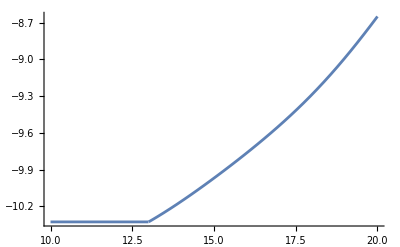

```mathematica
Plot[Log10[σωbar[Gstar]],{Gstar,10,20}]
```

To convert from angular resultion precision to distance precision, we have:
ϖ=a/D, where a = 1 AU

σϖ=-a/D^2σD

So that the magnitude of σD/D=σϖ*D/a

```mathematica
auInMpc=1.496*10^11*(3.241*10^-23)
Msun=4.83;
(*McepheidGaia=-5.903; (*Riess 22 Table 4*)*)
McepheidGaia=-6.05; (*https://arxiv.org/pdf/2208.09403 in G band*)
mFiducialStar[dMpc_]:=McepheidGaia+5*Log10[dMpc]+25
```

4.84854×10^-12

```mathematica
mFiducialStar[10*10^-3]
```

8.95

```mathematica
σDoverDParallax[dMpc_]:=σωbar[mFiducialStar[dMpc]]*dMpc/auInMpc
```

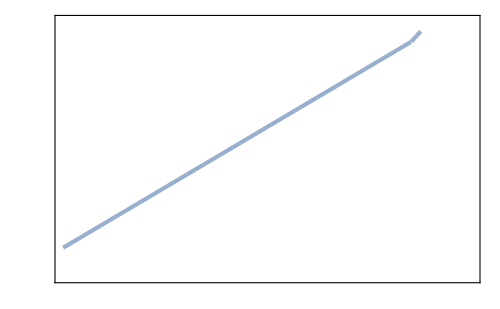

```mathematica
gaiaParallaxDistancePlot=Plot[Log10[σDoverDParallax[10^logdMpc]],{logdMpc,-8,-1},
PlotStyle->{{(*color[5]*)Lighter[color[1],.3],Opacity[.9],AbsoluteThickness[3]}},
Frame->True,Axes->False,PlotRange->{{-8,0},{-8,0.5}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_D/D",Magnification->1.5],None},{MaTeX["D \\, \\rm [Mpc]",Magnification->1.5],None}},
FrameTicks->{{logTick[-6,2,1.5,1],Automatic},{logTick[-6,0,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Other geometric distances

dMpc=10^((μ-25)/5)
σμ=5/Log[10]σd/d
σμReiss=σH/H=σd/d

```mathematica
(*From Detached Eclipsing Binaries DEBs*)
μLMC=18.493;
lmcDistance=10^((μLMC-25)/5);
lmcPrecisionDistance=1.2*1/100 ;
lmcPt={lmcDistance,lmcPrecisionDistance};
```

```mathematica
(*From Masers. *)
μNGC4258=29.387; (*http://arxiv.org/abs/1604.01424v3*)
NGC4258Distance=10^((μNGC4258-25)/5)
ngcPrecisionDistance=1.5*1/100 ;
ngcPt={NGC4258Distance,ngcPrecisionDistance};
```

7.5405

```mathematica
ngcPrecisionDistance*5/Log[10]
```

0.0325721

```mathematica
√(((.10)^2+(.17)^2)/7.54^2)*100
```

2.61579

```mathematica
(*From DEBs. http://arxiv.org/abs/1604.01424v3*)
μM31=24.36;
M31Distance=10^((μM31-25)/5)
M31PrecisionDistance=.08*Log[10]/5
m31Pt={M31Distance,M31PrecisionDistance}
```

0.744732

0.0368414

{0.744732,0.0368414}

```mathematica
μSMC=18.977;
SMCDistance=10^((μSMC-25)/5)
SMCPrecisionDistance=√((.016)^2+(.028)^2)*Log[10]/5
smcPt={SMCDistance,SMCPrecisionDistance}
```

0.062431

0.0148512

{0.062431,0.0148512}

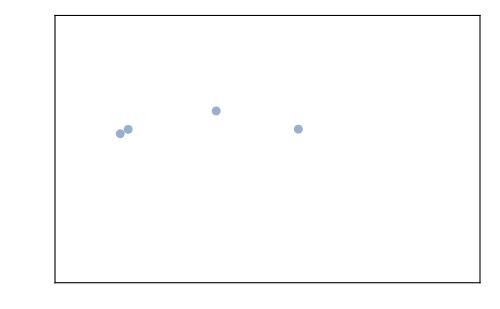

```mathematica
otherGeometricDistancePlot=ListPlot[{
Log10[lmcPt],
Log10[ngcPt],
Log10[m31Pt],
Log10[smcPt]
},Frame->True,Axes->False,PlotRange->{{-2,3},{-5,0.5}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
PlotStyle->{Lighter[color[1],.3],Opacity[.9]}(*Blend[{color[2],Orange},.75]*),
FrameLabel->{{MaTeX["\\sigma_D/D",Magnification->1.5],None},{MaTeX["D \\, \\rm [Mpc]",Magnification->1.5],None}},
FrameTicks->{{logTick[-6,2,1.5,1],Automatic},{logTick[-6,0,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Tip of the Red Giants

dMpc=10^((μ-25)/5)
σμ=5/Log[10]σd/d
σμReiss=σH/H=σd/d

```mathematica
(*From TRGB. *)
μNGC4203=27.36; (*https://arxiv.org/pdf/1906.08260*)
NGC4203Distance=10^((μNGC4203-25)/5);
NGC4203PrecisionDistance=.07*Log[10]/5;
NGC4203Pt={NGC4203Distance,NGC4203PrecisionDistance};
```

```mathematica
freedman24TGRBTable3=Import[NotebookDirectory[]<>"Data/TGRB_Freedman24.csv","Table"];
```

```mathematica
σDOverDCTGRB[δμ_]:=1/5*Log[10]δμ
dMpcTGRB[μ_]:=10^((μ-25)/5)
```

```mathematica
TGRBUncertaintyvsDistanceTab=Table[{
μTGRBi=freedman24TGRBTable3[[i,7]];
δμTGRBi=freedman24TGRBTable3[[i,8]];
dMpcTGRB[μTGRBi],σDOverDCTGRB[δμTGRBi]},{i,1,Length[freedman24TGRBTable3]}]
```

{{6.64661,0.013355},{31.6082,0.0322362},{19.5884,0.0184207},{19.5884,0.0184207},{19.5884,0.0184207},{18.7241,0.0184207},{18.7068,0.027631},{18.7068,0.027631},{18.3738,0.0174996},{18.3738,0.0174996},{21.3403,0.0446702},{27.8099,0.0230259},{11.5505,0.0184207},{28.4839,0.0230259},{11.0713,0.0184207},{22.3563,0.0313152},{21.5874,0.0193417},{15.4241,0.012434},{15.8343,0.0322362},{15.4454,0.0165786},{22.636,0.0336177},{23.3884,0.0216443},{13.0798,0.0179602},{13.0798,0.0179602},{21.1739,0.0216443}}

```mathematica
TGRBUncertaintyvsDistanceTab=Join[TGRBUncertaintyvsDistanceTab,{NGC4203Pt}]
```

{{6.64661,0.013355},{31.6082,0.0322362},{19.5884,0.0184207},{19.5884,0.0184207},{19.5884,0.0184207},{18.7241,0.0184207},{18.7068,0.027631},{18.7068,0.027631},{18.3738,0.0174996},{18.3738,0.0174996},{21.3403,0.0446702},{27.8099,0.0230259},{11.5505,0.0184207},{28.4839,0.0230259},{11.0713,0.0184207},{22.3563,0.0313152},{21.5874,0.0193417},{15.4241,0.012434},{15.8343,0.0322362},{15.4454,0.0165786},{22.636,0.0336177},{23.3884,0.0216443},{13.0798,0.0179602},{13.0798,0.0179602},{21.1739,0.0216443},{2.96483,0.0322362}}

```mathematica
TGRBUncertaintyvsDistanceTab=DeleteDuplicates[TGRBUncertaintyvsDistanceTab]
```

{{6.64661,0.013355},{31.6082,0.0322362},{19.5884,0.0184207},{18.7241,0.0184207},{18.7068,0.027631},{18.3738,0.0174996},{21.3403,0.0446702},{27.8099,0.0230259},{11.5505,0.0184207},{28.4839,0.0230259},{11.0713,0.0184207},{22.3563,0.0313152},{21.5874,0.0193417},{15.4241,0.012434},{15.8343,0.0322362},{15.4454,0.0165786},{22.636,0.0336177},{23.3884,0.0216443},{13.0798,0.0179602},{21.1739,0.0216443},{2.96483,0.0322362}}

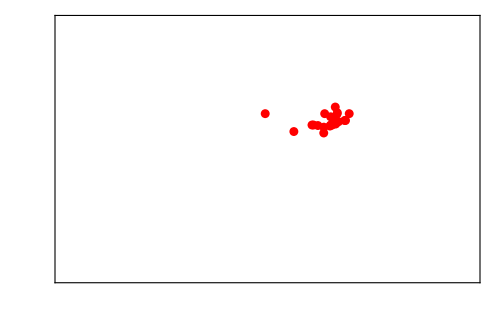

```mathematica
TRGBDistancePlot=ListPlot[
Log10[TGRBUncertaintyvsDistanceTab]
,Frame->True,Axes->False,PlotRange->{{-2,3},{-5,0.5}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},
PlotStyle->Red(*xgfsnormal6TabColors[[3]]*),
FrameLabel->{{MaTeX["\\sigma_D/D",Magnification->1.5],None},{MaTeX["D \\, \\rm [Mpc]",Magnification->1.5],None}},
FrameTicks->{{logTick[-6,2,1.5,1],Automatic},{logTick[-6,3,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Cepheids

```mathematica
reissTable6=Import[NotebookDirectory[]<>"Data/cepheid_distances_Reiss.txt","Table"];
```

```mathematica
reissTable6Transpose=Transpose[reissTable6];
```

```mathematica
galaxyμTab=reissTable6Transpose[[6]]
```

{29.193,32.922,34.531,32.846,33.719,32.57,32.546,31.379,31.29,31.29,31.501,31.457,32.067,32.629,32.474,33.044,33.044,33.044,32.332,32.123,31.939,32.808,31.644,31.724,31.615,30.856,30.838,31.818,32.606,33.12,33.12,31.775,30.569,30.569,33.116,32.232,32.363,31.628,33.274,32.504,33.196,32.849}

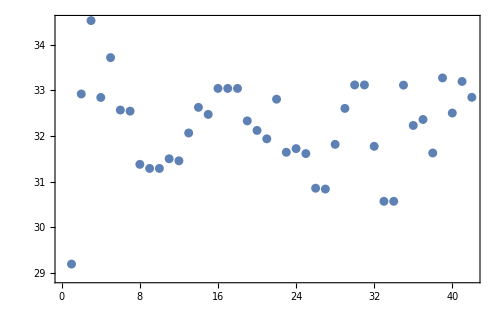

```mathematica
ListPlot[galaxyμTab,
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\mu",Magnification->1.5],None},{MaTeX["\\text{Galaxy}",Magnification->1.5],None}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

```mathematica
galaxyσμTab=reissTable6Transpose[[7]]
```

{0.039,0.124,0.253,0.109,0.151,0.075,0.06,0.057,0.037,0.037,0.062,0.065,0.1,0.155,0.16,0.165,0.165,0.165,0.077,0.052,0.035,0.081,0.09,0.072,0.117,0.13,0.051,0.085,0.208,0.075,0.075,0.053,0.05,0.05,0.207,0.101,0.122,0.126,0.116,0.121,0.155,0.068}

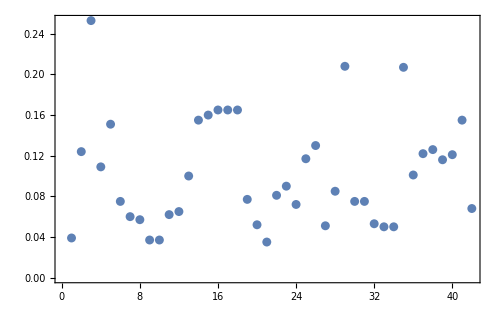

```mathematica
ListPlot[galaxyσμTab,
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_\\mu",Magnification->1.5],None},{MaTeX["\\text{Galaxy}",Magnification->1.5],None}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

```mathematica
σDOverDCepheid[δμ_]:=1/5*Log[10]δμ
```

```mathematica
σDOverDCepheid[.2]
```

0.0921034

```mathematica
Mcepheid=-5.894;
mCepheid[μCepheid_]:=μCepheid+Mcepheid
```

```mathematica
dMpcCepheid[μ_]:=10^((μ-25)/5)
```

```mathematica
cepheidDvsσDOverDTab=Table[{dMpcCepheid[galaxyμTab[[i]]],σDOverDCepheid[galaxyσμTab[[i]]]},{i,1,Length[galaxyσμTab]}]
```

{{6.89604,0.0179602},{38.4061,0.0571041},{80.5749,0.116511},{37.0851,0.0501964},{55.437,0.0695381},{32.6588,0.0345388},{32.2998,0.027631},{18.8712,0.0262495},{18.1134,0.0170391},{18.1134,0.0170391},{19.9618,0.0285521},{19.5614,0.0299336},{25.906,0.0460517},{33.5583,0.0713801},{31.2464,0.0736827},{40.6256,0.0759853},{40.6256,0.0759853},{40.6256,0.0759853},{29.2685,0.0354598},{26.5828,0.0239469},{24.4231,0.0161181},{36.4418,0.0373019},{21.3206,0.0414465},{22.1208,0.0331572},{21.0378,0.0538805},{14.832,0.0598672},{14.7096,0.0234864},{23.0994,0.0391439},{33.2047,0.0957875},{42.0727,0.0345388},{42.0727,0.0345388},{22.6464,0.0244074},{12.9957,0.0230259},{12.9957,0.0230259},{41.9952,0.095327},{27.9512,0.0465122},{29.6893,0.0561831},{21.1641,0.0580251},{45.1648,0.05342},{31.6811,0.0557226},{43.5712,0.0713801},{37.1364,0.0313152}}

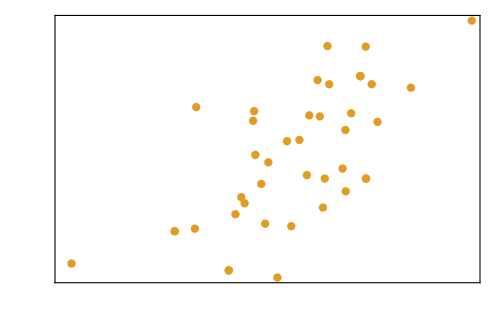

```mathematica
cepheidDistancePlot=ListPlot[Log10[cepheidDvsσDOverDTab],
Frame->True,Axes->False,PlotRange->All,
PlotStyle->{{(*color[3]*)color[2],AbsolutePointSize[6]}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm cepheids}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-2,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Hubble Flow SNe

```mathematica
avgSNmagScatter=0.135;
avgSNDistanceScatter=1/5*Log[10]avgSNmagScatter
```

0.0621698

```mathematica
dMpcSN1a[μ_]:=10^((μ-25)/5)
```

```mathematica
sne1aσDoverDTab=Table[
{dMpcSN1a[μIterator],avgSNDistanceScatter},{μIterator,33.5,43.6,.1}];
```

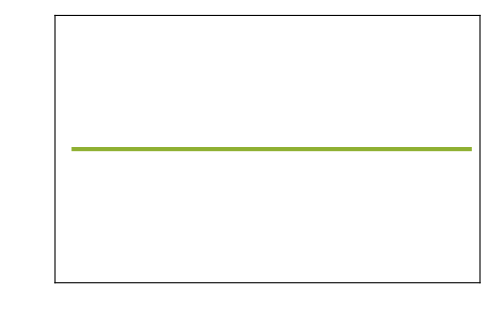

```mathematica
sne1aHubbleFlowDistancePlot=ListPlot[Log10[sne1aσDoverDTab],
Frame->True,Axes->False,PlotRange->All,Joined->True,InterpolationOrder->1,
PlotStyle->{{(*Darker[xgfsnormal6TabColors[[7]],.1]*)color[3],AbsoluteThickness[3]}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm Ia}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-2,3,1.5,1],Automatic},{logTick[-2,4,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### EEM SN Type II

```mathematica
σtIII=3; (*Subscript[σ, t] for phase III in ps*)
σtII=10; (*Subscript[σ, t] for phase II in ps*)
RIII=2*10^4; (*Spectral resolution for phase III*)
RII=1*10^4;(*Spectral resolution for phase II*)
nIII=10;(*Number pair arrays for phase III*)
nII=1;(*Number pair arrays for phase II*)

telescopeRadiusII=5;(*Telescope radius in meters of phase II*)
telescopeRadiusIII=5;(*Telescope radius in meters of phase III*)

efficiencyFactor=1/2;

figureOfMerit[σtps_,Rspectral_,nArr_,telescopeRadius_,efficiency_]:=σtps^(-1/2)Rspectral^(1/2)nArr*(π*telescopeRadius^2)*efficiency
```

```mathematica
figureOfMeritStnd=figureOfMerit[σtII,RII,nII,telescopeRadiusII,efficiencyFactor]//N
```

1241.82

```mathematica
matchLightStnd=figureOfMeritStnd
```

1241.82

```mathematica
lowMatchlightPaper=1250;
highMatchlightPaper=5*10^4;
```

```mathematica
MTypeII=-16.1;
(*MTypeIa=-18.5;*)
mTypeII[dMPc_]:=MTypeII+5*Log10[dMPc]+25;
```

```mathematica
σDoverDEEMTypeII[matchlight_,dMpc_,tObshour_]:=6.3*10^-2*10^(0.4*(mTypeII[dMpc]-12.5))*(tObshour/6)^(-1/2)(matchlight/matchLightStnd)^-1
```

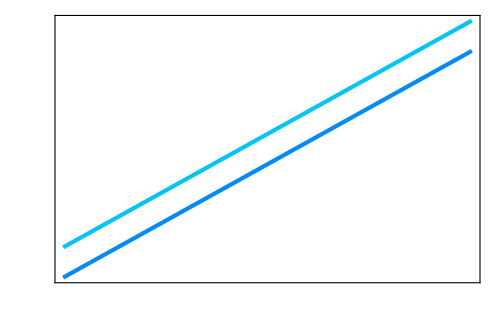

```mathematica
(*eemInferredDistanceTypeIIPlot=Plot[{
Log10[σDoverDEEMTypeII[matchLightLow,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeII[matchLightMidRange,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeII[matchLightSuper,10^logdMpc,6*30]]
},{logdMpc,-2,4},
PlotStyle->{
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3]},
{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3]}
},
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm EEM}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-5,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]*)

eemInferredDistanceTypeIIPlot=Plot[{
Log10[σDoverDEEMTypeII[lowMatchlightPaper,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeII[highMatchlightPaper,10^logdMpc,6*30]]
},{logdMpc,-2,4},
PlotStyle->{
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3]},
{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3]}
},
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm EEM}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-5,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### EEM SN Type Ia

```mathematica
(*MTypeII=-16.1;*)
MTypeIa=-18.5;
mTypeIa[dMPc_]:=MTypeIa+5*Log10[dMPc]+25;
```

```mathematica
σDoverDEEMTypeIa[matchlight_,dMpc_,tObshour_]:=6.3*10^-2*10^(0.4*(mTypeIa[dMpc]-12.0))*(tObshour/6)^(-1/2)(matchlight/matchLightStnd)^-1
```

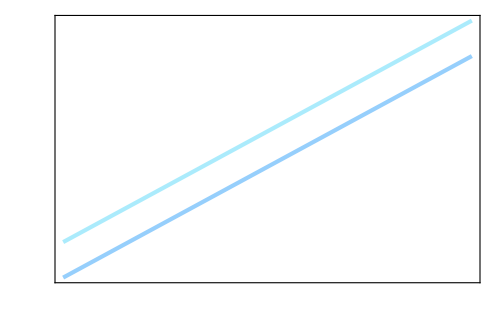

```mathematica
snIaOpacity=0.33;
(*eemInferredDistanceTypeIaPlot=Plot[{
Log10[σDoverDEEMTypeIa[matchLightLow,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeIa[matchLightMidRange,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeIa[matchLightSuper,10^logdMpc,6*30]]
},{logdMpc,-1,4},
PlotStyle->{
(*{xgfsnormal12TabColors[[10]],AbsoluteThickness[3],Dashed},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3],Dashed},{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3],Dashed}*)
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3],Opacity[snIaOpacity]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3],Opacity[snIaOpacity]},{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3],Opacity[snIaOpacity]}
},
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm EEM}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-5,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]*)

eemInferredDistanceTypeIaPlot=Plot[{
Log10[σDoverDEEMTypeIa[lowMatchlightPaper,10^logdMpc,6*30]],
Log10[σDoverDEEMTypeIa[highMatchlightPaper,10^logdMpc,6*30]]
},{logdMpc,-1,4},
PlotStyle->{
{xgfsnormal12TabColors[[10]],AbsoluteThickness[3],Opacity[snIaOpacity]},
{xgfsnormal12TabColors[[3]],AbsoluteThickness[3],Opacity[snIaOpacity*1.25]},{Lighter[xgfsdark6TabColors[[2]],.25],AbsoluteThickness[3],Opacity[snIaOpacity]}
},
Frame->True,Axes->False,PlotRange->All,
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm EEM}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-5,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Intrinsic Uncertainty of Cepheids

For the jth de-reddened cepheid magnitude mHij in the ith host with period Pij and metallicity [O/H]ij, we Haversine
mW,ij = μ0,i + MH1 + bw*(log Pij - 1) + Zw[O/H]ij

which is Eq 1 of Riess

Once an anchor is determined, the corrected absolute magnitude is
MW,j = mw,anchor,j-μAnchor + Δμanchor

and MW,1 = -5.894 ±0.017 mag is determined

```mathematica
σμNGC258=1.5*10^-2;
fiducialAnchorDistanceMpc=10;
```

```mathematica
cepheidCalibratedDistanceTab=Table[
cepheidDistanceI=cepheidDvsσDOverDTab[[i,1]];
σDoverDi=cepheidDvsσDOverDTab[[i,2]];
subtractedσDoverDiSq=σDoverDi^2-σμNGC258^2;
newσDoverDi=√(subtractedσDoverDiSq+0*σDoverDEEMTypeII[matchLightMidRange,(*cepheidDistanceI*)fiducialAnchorDistanceMpc,6*30]^2);
{cepheidDistanceI,newσDoverDi},{i,1,Length[cepheidDvsσDOverDTab]}]
```

{{6.89604,0.00987763},{38.4061,0.0550988},{80.5749,0.115541},{37.0851,0.0479028},{55.437,0.067901},{32.6588,0.0311115},{32.2998,0.023205},{18.8712,0.0215415},{18.1134,0.00808282},{18.1134,0.00808282},{19.9618,0.0242944},{19.5614,0.0259041},{25.906,0.0435403},{33.5583,0.0697863},{31.2464,0.0721398},{40.6256,0.07449},{40.6256,0.07449},{40.6256,0.07449},{29.2685,0.032131},{26.5828,0.0186669},{24.4231,0.00589856},{36.4418,0.034153},{21.3206,0.038637},{22.1208,0.0295703},{21.0378,0.0517504},{14.832,0.0579576},{14.7096,0.0180723},{23.0994,0.0361559},{33.2047,0.0946058},{42.0727,0.0311115},{42.0727,0.0311115},{22.6464,0.0192541},{12.9957,0.0174697},{12.9957,0.0174697},{41.9952,0.0941395},{27.9512,0.0440271},{29.6893,0.0541437},{21.1641,0.0560528},{45.1648,0.0512708},{31.6811,0.0536657},{43.5712,0.0697863},{37.1364,0.0274889}}

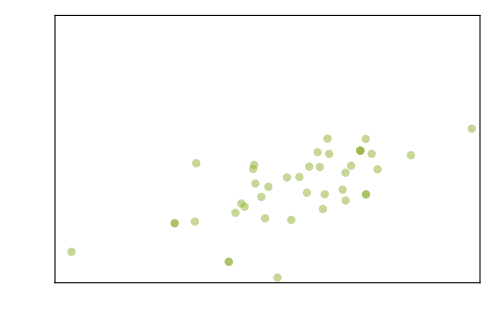

```mathematica
cepheidCalibratedDistancePlot=ListPlot[Log10[cepheidCalibratedDistanceTab],
Frame->True,Axes->False,PlotRange->All,
PlotStyle->{{color[3],AbsolutePointSize[6],Opacity[.5]}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm cepheids}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-2,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Intrinsic Uncertainty of TGRB

```mathematica
σμNGC258=1.5*10^-2;
fiducialAnchorDistanceMpc=10;
```

```mathematica
lmcPrecisionDistance
```

0.012

```mathematica
M31PrecisionDistance
```

0.0368414

```mathematica
ngcPrecisionDistance
```

0.015

```mathematica
smcPrecisionDistance
```

smcPrecisionDistance

```mathematica
σtotalAnchorCalibrator=(1/lmcPrecisionDistance^2+1/M31PrecisionDistance^2+1/ngcPrecisionDistance^2+1/SMCPrecisionDistance^2)^(-1/2)
```

0.00774761

```mathematica
tgrbCalibratedDistanceTab=Table[
TGRBDistanceI=TGRBUncertaintyvsDistanceTab[[i,1]];
σDoverDi=TGRBUncertaintyvsDistanceTab[[i,2]];
subtractedσDoverDiSq=σDoverDi^2-σtotalAnchorCalibrator^2;
newσDoverDi=√(subtractedσDoverDiSq);
{TGRBDistanceI,newσDoverDi},{i,1,Length[TGRBUncertaintyvsDistanceTab]}]
```

{{6.64661,0.010878},{31.6082,0.0312913},{19.5884,0.0167122},{18.7241,0.0167122},{18.7068,0.0265226},{18.3738,0.0156911},{21.3403,0.0439931},{27.8099,0.0216833},{11.5505,0.0167122},{28.4839,0.0216833},{11.0713,0.0167122},{22.3563,0.0303416},{21.5874,0.0177222},{15.4241,0.00972511},{15.8343,0.0312913},{15.4454,0.0146569},{22.636,0.0327128},{23.3884,0.0202102},{13.0798,0.0162031},{21.1739,0.0202102},{2.96483,0.0312913}}

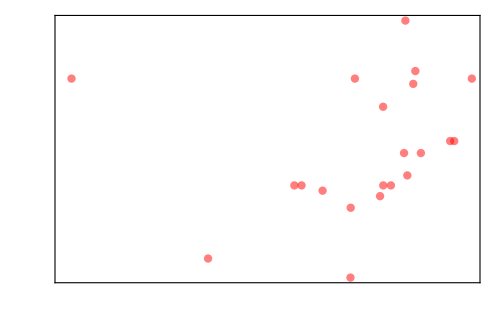

```mathematica
tgrbCalibratedDistancePlot=ListPlot[Log10[tgrbCalibratedDistanceTab],
Frame->True,Axes->False,PlotRange->All,
PlotStyle->{Red,AbsolutePointSize[6],Opacity[.5]},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm cepheids}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},
FrameTicks->{{logTick[-2,2,1.5,1],Automatic},{logTick[-2,2,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Intrinsic Uncertainty of SN Ia

```mathematica
avgSNmagScatter=0.135;
avgSNDistanceScatter=1/5*Log[10]avgSNmagScatter
```

0.0621698

```mathematica
avgSNDistanceScatter/(√277)*100 (*Avg SN uncertainty divided by √N=√277 SN matches the σm−z of Riess Table 7 of 0.4%*)
```

0.373542

```mathematica
σμNonSN=√(((.7)/100)^2+((.9)/100)^2+((.3)/100)^2)(*Subtract out the anchor and cepheid uncertainties. Note, much smaller*)
```

0.0117898

```mathematica
intrinsicSNUncertainty=√(avgSNDistanceScatter^2-σμNonSN^2)
```

0.0610417

```mathematica
snCalibratedDistance1Tab=Table[
snIaDistanceI=sne1aσDoverDTab[[i,1]];
newσDoverDi=√(intrinsicSNUncertainty^2+0*σDoverDEEMTypeIa[matchLightMidRange,(*cepheidDistanceI*)fiducialAnchorDistanceMpc,6*30]^2);
{snIaDistanceI,newσDoverDi},{i,1,Length[sne1aσDoverDTab]}];
```

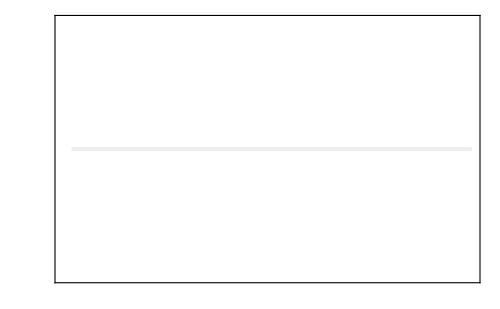

```mathematica
snCalibratedDistance1Plot=ListPlot[Log10[snCalibratedDistance1Tab],
Frame->True,Axes->False,PlotRange->All,
Joined->True,
PlotStyle->{{xgfsnormal6TabColors[[7]],AbsoluteThickness[3],Opacity[.3]}},BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["(\\sigma_D/D)_{\\rm Ia}",Magnification->1.5],None},{MaTeX["\\text{Distance [Mpc]}",Magnification->1.5],None}},FrameTicks->{{logTick[-2,3,1.5,1],Automatic},{logTick[-2,4,1.5,1],Automatic}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500]
```

#### Combined CDL Plot

```mathematica
canvasPlot=Plot[Null,{logdMpc,-5,5},Frame->True,Axes->False,PlotRange->{{-4,3},{-3.5,-0.5}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_D/D",Magnification->1.5],None},{MaTeX["D_L \\, \\rm [Mpc]",Magnification->1.5],None}},
FrameTicks->{{logTick[-6,2,1.5,1],Automatic},{logTick[-6,5,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500,AspectRatio->1/2]
```

-Graphics-

```mathematica
canvasPlot2=Plot[Null,{logdMpc,-5,5},Frame->True,Axes->False,PlotRange->{{-3,3},{-2,-0.5}},
BaseStyle->{FontSize->17,FontFamily->"Latin Modern Roman"},FrameLabel->{{MaTeX["\\sigma_D/D",Magnification->1.5],None},{MaTeX["D_L \\, \\rm [Mpc]",Magnification->1.5],None}},
FrameTicks->{{logTick[-6,2,1.5,1],Automatic},{logTick[-6,5,1.5,1],Automatic}},
FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],ImageSize->500,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

-Graphics-

```mathematica
distancePrecisionComparisonPlot=Show[canvasPlot,eemInferredDistanceTypeIIPlot,eemInferredDistanceTypeIaPlot,gaiaParallaxDistancePlot, otherGeometricDistancePlot,sne1aHubbleFlowDistancePlot,(*snCalibratedDistance1Plot,*)
cepheidDistancePlot,(*cepheidCalibratedDistancePlot,*)TRGBDistancePlot,(*tgrbCalibratedDistancePlot,*)Epilog->{
Inset[Style[Rotate[changeStyle[Lighter[color[1],.1]]@MaTeX["\\textit{Gaia } \\text{Parallax}",Magnification->1.3],50Degree]],Scaled[{.15,.58}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{LMC}",Magnification->1.3],0Degree]],Scaled[{.385-.025,.3+.15}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{SMC}",Magnification->1.3],0Degree]],Scaled[{.385-.01,.3+.15+.16}]],
Inset[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{M31}",Magnification->1.3],0Degree]],Scaled[{.55,.46+.28}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[1],.2]]@MaTeX["\\text{NGC4258}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[.65]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.505+.01,.57}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[Red,.3]]@MaTeX["\\text{TRGB}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[.75]],FrameStyle->None,FrameMargins->{{-2.5,-2.5},{-2.5,-2.5}}],Scaled[{.805,.53}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[(*color[2]*)Orange,.3]]@MaTeX["\\text{Cepheids}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[.75]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.7,.83+.01}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[(*xgfsnormal6TabColors[[7]]*)color[3],.3]]@MaTeX["\\text{SNIa}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[1]],FrameStyle->None,FrameMargins->{{-2.5,-2.5},{-7.5,-2.5}}],Scaled[{.9+.025,.8205}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],.3]]@MaTeX["\\text{EEM}_{\\#1}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[1]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.475+.075+.015+.055,.125-.01}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[3]],.3]]@MaTeX["\\text{EEM}_{\\#2}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[1]],FrameStyle->None,FrameMargins->{{None,None},{-3,-3}}],Scaled[{.475+.21+.015+.045,.125-.01}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],.3]]@MaTeX["\\text{SN IIP}",Magnification->.9],68 Degree]],Scaled[{.47+.07+.006+.06,.27}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[10]],.3]]@MaTeX["\\text{SN Ia}",Magnification->.9],68 Degree]],Scaled[{.47+.06+.0775+.02-.02+.05,.27-.01}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[3]],.3]]@MaTeX["\\text{SN IIP}",Magnification->.9],68 Degree]],Scaled[{.58+.084+.045+.01,.27}]],
Inset[Style[Rotate[changeStyle[Darker[xgfsnormal12TabColors[[3]],.3]]@MaTeX["\\text{SN Ia}",Magnification->.9],68 Degree]],Scaled[{.58+.06+.0875+.02-.02+.045,.27-.01}]],
{(*Darker[(*Orange*)color[1],0]*)Lighter[color[1],.3],Opacity[.9],AbsoluteThickness[1.5],Arrowheads[.03],Arrow[{Scaled[{.59+.01,.56}],Scaled[{.685,.56}]}]}
},ImageSize->500,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/distanceComparisonPlot.pdf",distancePrecisionComparisonPlot]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/distanceComparisonPlot.pdf

## Lagrange Multiplier Optimum CDL Rungs

### Lagrange Multiplier Approach

Let  xi^2=(σDOverD(m,t))^2+σCepheid(m)^2

where σDOverD(m,t)=σDOverD(m,t0)*(t0/t)^(-1/2), where σDOverD(m,t0) =6.3*10^-2*10^(0.4(m-12.0))*1/ML, and t0=6hrs and ML = (σt/(10ps))^(1/2)*(A/(π*(5m)^2))^-1*(R/10^4)^(-1/2)*(narr/1)^-1
and 
σCepheid(m)≈(0.5*10^-2);


Maximize the sum ∑1/xi^2=∑1/(xi(mi,ti)^2), under the constraint that ∑ti=tyr 
or whatever fraction of a year is used for observation time, like 1/4 of a year etc



Let L=∑1/(xi(mi,ti)^2)-λ*(∑ti-tyr)

(∂L)/(∂ti)=∂/(∂ti)(∑1/(xj(mj,tj)^2)-λ*(∑tj-tyr))
=-2/(xi(mi,ti)^3)(∂xi)/(∂ti)-λ=0
-1/(xi(mi,ti)^4)(∂xi^2)/(∂ti)-λ=0
and

(∂L)/(∂λ)=-(∑ti-tyr)=0


The first equation implies
λ=-1/(xi(mi,ti)^4)(∂xi^2)/(∂ti)=-1/(((σDOverD(m))^2+σCepheid(m)^2)^2)(-(σDoverD(t0))^2 t0/ti^2)
=1/(((σDOverD(t0))^2*t0/ti+σCepheid(m)^2)^2)((σDoverD(t0))^2 t0/ti^2)

```mathematica
Solve[1/(((σDoverDt0)^2*t0/ti+σCalibrator^2)^2)(σDoverDt0)^2 t0/ti^2==λ,ti]//FullSimplify
```

{{ti→-((√t0 σDoverDt0)/(√λ)+t0 σDoverDt0^2)/σCalibrator^2},{ti→((√t0 σDoverDt0)/(√λ)-t0 σDoverDt0^2)/σCalibrator^2}}

Taking the positive root, we have ti=(√t0 σDoverDt0 - t0 √λ σDoverDt0^2)/(√λ σCalibrator^2)=1/σCalibrator^2((√t0*σDoverDt0)/(√λ)-(√t0*σDoverDt0)^2)
Let 
σ1=√t0 σDoverDt0
σ2=σCalibrator

so that 
ti=(σ1[i]/(√λ)- σ1[i]^2)/σ2[i]^2

Now, plugging this into the constraint equation(∑ti-tyr)=0, we have

∑(σ1/(√λ)- σ1^2)/σ2^2=tyr

or equivalently,

1/(√λ)∑σ1/σ2^2-∑σ1^2/σ2^2=tyr

ie

1/(√λ)=(tyr+∑σ1^2/σ2^2)/(∑σ1/σ2^2) where the sum is over the different m


Finally, this implies the time that SNi should be looked at is

ti=(σ1[i]/(√λ)- σ1[i]^2)/σ2[i]^2==((tyr+∑σ1^2/σ2^2)/(∑σ1/σ2^2))*σ1[i]/σ2[i]^2-σ1[i]^2/σ2[i]^2
=(tyr+∑(^(t0*σDoverDt0[j]^2))/σCalibrator[j]^2)*(^(√t0*σDoverDt0[i])/σCalibrator[i]^2)/(∑^(√t0*σDoverDt0[j])/σCalibrator[j]^2)-(^(t0*σDoverDt0[i]^2))/σCalibrator[i]^2
==(tyr+∑(^(t0*σDoverDt0[j]^2))/σCalibrator[j]^2)*(^σDoverDt0[i]/σCalibrator[i]^2)/(∑^σDoverDt0[j]/σCalibrator[j]^2)-(^(t0*σDoverDt0[i]^2))/σCalibrator[i]^2

### Generating SN Distribution

CDF[m]=A∫^m f(m')dm'=A*10^(b(m-m0))
PDF[m]=d(CDF[m])/dm=

```mathematica
D[1/a*10^(b*(m-m0)),m]
```

(10^(b (m-m0)) b Log[10])/a

WLOG, define then pdf[m]=f[m]=1/a 10^(b(m-m0)), where b = .505, m0=12.0 is a best fit

Non-normalized PDF is 

f(m)=b*Log[10]/a*10^(b(m-m0))

```mathematica
pdf[m_]:=(b*Log[10])/a*10^(b*(m-m0))
```

```mathematica
Integrate[10^(b(mp-m0)),{mp,-∞,m}]
```

ConditionalExpression[10^(b (m-m0))/(b Log[10]), Re[b]>0]

```mathematica
totalSNIntegral=FullSimplify[Integrate[pdf[m],{m,-∞,mf}],b>0]
```

10^(b (-m0+mf))/a

```mathematica
aNormalization=a/.First[Solve[totalSNIntegral==1,a]]
```

10^(b (-m0+mf))

```mathematica
normalizedPDF[b_,m_,m0_,mf_]=FullSimplify[pdf[m]/.{a->aNormalization}]
```

10^(b (m-mf)) b Log[10]

```mathematica
b*Log[10]/10^(b*(mf-m0))10^(b(m-m0))//FullSimplify
```

10^(b (m-mf)) b Log[10]

```mathematica
Integrate[normalizedPDF[b,m,m0,mf],{m,-∞,mf}]
```

ConditionalExpression[1, Re[b]>0]

```mathematica
Integrate[a*normalizedPDF[b,mprime,m0,mf],{mprime,-∞,m}]
```

ConditionalExpression[10^(b (m-mf)) a, Re[b]>0]

```mathematica
b0CDF=0.505;
m0CDF=12.0;
typeIIFraction=.17;(*Mag-limited fraction of SN that are typeII. From Table 7 of http://arxiv.org/abs/1006.4612v2*)
subtypeFraction=0.30(*+0.25+0.15*); (*IIP+IIL+IIb. Fraction of TypeII that are IIP, IIL, IIb, from same table.*)
```

```mathematica
typeIIFraction*subtypeFraction
```

0.051

```mathematica
typeIaFraction=.79;
```

```mathematica
snYearRealization[m0_,mff_,b_,SNfraction_]:=
(dPDF=ProbabilityDistribution[normalizedPDF[b,m,m0,mff],{m,-∞,mff}];
aFactor=10^(b(mff-m0));
RandomVariate[dPDF,Round[aFactor*SNfraction]])
```

```mathematica
snYearRealization[m0CDF,14,b0CDF,typeIIFraction*subtypeFraction]
```

RandomVariate[ProbabilityDistribution[1.16281 10^(0.505 (-14+x)),{x,-∞,14}],1]

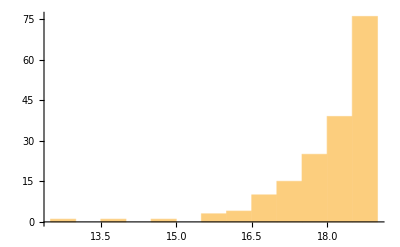

```mathematica
exSNRealization=snYearRealization[m0CDF,19,b0CDF,typeIIFraction*subtypeFraction];
Histogram[exSNRealization]
```

### σμ Optimization for Cepheids (with max observation cutoff)

```mathematica
σDoverDt0[m_,snrEnhancement_]:=6.3*10^-2*10^(0.4(m-12.0))*1/snrEnhancement
```

```mathematica
σCalibratorCepheid[m_]:=.5*10^-2;
```

```mathematica
t0hr=6;
```

```mathematica
numTrials=25(*50*)(*500*);
numYrs=5;
snPopulationTrialsTypeII=Table[Sort[
Flatten[Table[
snYearRealization[m0CDF,19,b0CDF,typeIIFraction*subtypeFraction]
,{yrs,1,numYrs}]]
],{i,1,numTrials}];
```

```mathematica
tiLangrangeMultiplierCepheid[inputSNList_,tTotalObservationhr_,snrEnhancement_]:=(
snPopList=inputSNList;
sum1UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σCalibratorCepheid[snPopList[[i]]])^2 t0hr,{i,1,Length[snPopList]}];
sum2UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σCalibratorCepheid[snPopList[[i]]]^2),{i,1,Length[snPopList]}];
tiIdealCepheidsTab=Table[
mi=snPopList[[i]];
ti=(tTotalObservationhr+sum1UncertaintyRatio)*(σDoverDt0[mi,snrEnhancement]/σCalibratorCepheid[mi]^2)/sum2UncertaintyRatio-(σDoverDt0[mi,snrEnhancement]/σCalibratorCepheid[mi])^2*t0hr;
{mi,ti},{i,1,Length[snPopList]}]
)
```

```mathematica
tiIdealCepheidsList[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0,numOftPlateauSN_:0,fiducialNumSN_:-1]:=(

If[trialNum==0,snPop=Sort[snYearRealization[m0CDF,19,b0CDF,typeIIFraction*subtypeFraction]],snPop=snPopulationTrialsTypeII[[trialNum]][[numOftPlateauSN+1;;fiducialNumSN]]];

tiTimesPositiveDefinite=False;
snListLength=Length[snPop];
reducedSNPopList=snPop;


While[
tiTimesPositiveDefinite===False,
newtiTab=tiLangrangeMultiplierCepheid[reducedSNPopList,tTotalObservationhr,snrEnhancement];
observationTimeofBrightestSN=newtiTab[[-1]][[2]];
If[observationTimeofBrightestSN<=0,reducedSNPopList=Drop[reducedSNPopList,-1];,tiTimesPositiveDefinite=True];
];
newtiTab
)
```

```mathematica
σDoverDt[m_,snrEnhancement_,t_]:=σDoverDt0[m,snrEnhancement]*(t/t0hr)^(-1/2)
```

```mathematica
σμCepheids[inputSNList_,snrEnhancement_]:=(
snPopList=inputSNList;
σμIdealCepheid=(Sum[1/((σDoverDt[snPopList[[i,1]],snrEnhancement,snPopList[[i,2]]])^2+σCalibratorCepheid[snPopList[[i,1]]]^2),{i,1,Length[snPopList]}])^(-1/2)
)
```

```mathematica
tPlateauTypeII=3*30*6;
numOftPlateauSN=0;
```

```mathematica
redoIdealσμHistogramCepheids[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestSN=Max[snPopList[[;;,2]]];
totalObsTimeForOptimization=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialSN=Length[snPopList];
numOftPlateauSN=0;
updatedtiIdealCepheidsList=snPopList;
While[tObsOfBrightestSN>tPlateauTypeII,
numOftPlateauSN=numOftPlateauSN+1;
updatedtiIdealCepheidsList=tiIdealCepheidsList[totalObsTimeForOptimization-tPlateauTypeII,snrEnhancement,trialNum,numOftPlateauSN,numOfFiducialSN+30];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestSN=Max[updatedtiIdealCepheidsList[[;;,2]]];
totalObsTimeForOptimization=Sum[updatedtiIdealCepheidsList[[i,2]],{i,1,Length[updatedtiIdealCepheidsList]}];
numOfFiducialSN=Length[updatedtiIdealCepheidsList];
];
plateauSNTab=Table[{snPopulationTrialsTypeII[[trialNum,i]],tPlateauTypeII},{i,1,numOftPlateauSN}];
Join[plateauSNTab,updatedtiIdealCepheidsList]
(*{snPopList,updatedtiIdealCepheidsList}*)
)]
```

```mathematica
idealσμHistogramCepheids[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
(*idealSNPopulation=tiIdealCepheidsList[tTotalObservationhr,snrEnhancement,0];*)
idealSNPopulation=tiIdealCepheidsList[tTotalObservationhr,snrEnhancement,i];
idealSNPopulationPlateau=redoIdealσμHistogramCepheids[idealSNPopulation,snrEnhancement,i];
σμCepheids[idealSNPopulationPlateau,snrEnhancement],
{i,1,numTrials}]
)
```

```mathematica
snrEnhancementTab=Table[10^logSNREnhancement,{logSNREnhancement,-1.1,2.5,.1}]
```

{0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228}

```mathematica
oneσLowerQuantile=.5-.341
oneσUpperQuantile=.5+.341
```

0.159

0.841

```mathematica
matchlightCepheidCDL[tTotalObservationhr_?NumericQ]:=(
ParallelTable[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramTabSNRCepheids=idealσμHistogramCepheids[tTotalObservationhr,snrEnhancementIterator];
{snrEnhancementIterator,{Mean[histogramTabSNRCepheids],Quantile[histogramTabSNRCepheids,{oneσLowerQuantile,oneσUpperQuantile}](*StandardDeviation[histogramTabSNRCepheids]*)}},
{i,1,Length[snrEnhancementTab]}]
)
```

```mathematica
matchlightCepheidCDLTab=matchlightCepheidCDL[365*6*numYrs]
```

{{0.0794328,{0.125706,{0.0288469,0.22865}}},{0.1,{0.0999194,{0.0231095,0.181626}}},{0.125893,{0.0794529,{0.0186,0.144276}}},{0.158489,{0.0632152,{0.0150756,0.114608}}},{0.199526,{0.05034,{0.0123441,0.0910433}}},{0.251189,{0.0401389,{0.0102519,0.0723273}}},{0.316228,{0.0320643,{0.00867421,0.0574629}}},{0.398107,{0.0256803,{0.00750691,0.0456586}}},{0.501187,{0.0206393,{0.0066604,0.0362858}}},{0.630957,{0.0166634,{0.00605616,0.0288453}}},{0.794328,{0.0135301,{0.00552709,0.0229409}}},{1.,{0.0110606,{0.00504803,0.0182579}}},{1.25893,{0.0091117,{0.00477503,0.014547}}},{1.58489,{0.00756848,{0.00449839,0.0116101}}},{1.99526,{0.00633974,{0.00417342,0.00929024}}},{2.51189,{0.00535388,{0.00387578,0.0074629}}},{3.16228,{0.00455566,{0.00328693,0.00602884}}},{3.98107,{0.00390337,{0.00310835,0.00490859}}},{5.01187,{0.00336614,{0.00280364,0.0040377}}},{6.30957,{0.00292137,{0.00248133,0.00336324}}},{7.94328,{0.00255235,{0.00220919,0.00284142}}},{10.,{0.00224645,{0.00198177,0.00250282}}},{12.5893,{0.00199372,{0.00179221,0.00217941}}},{15.8489,{0.00178603,{0.00161028,0.00190945}}},{19.9526,{0.00161568,{0.00147143,0.0017377}}},{25.1189,{0.00146957,{0.00133693,0.00159768}}},{31.6228,{0.00133422,{0.00122261,0.00147526}}},{39.8107,{0.0012136,{0.00112347,0.00133005}}},{50.1187,{0.00110875,{0.0010364,0.00120937}}},{63.0957,{0.00101345,{0.000955256,0.00109166}}},{79.4328,{0.000926755,{0.000879645,0.000992308}}},{100.,{0.000847824,{0.000809251,0.000893914}}},{125.893,{0.0007759,{0.000742829,0.000810862}}},{158.489,{0.000710098,{0.000680623,0.000736381}}},{199.526,{0.000649705,{0.000622933,0.000670105}}},{251.189,{0.000594333,{0.00057033,0.000610929}}},{316.228,{0.000543778,{0.000522819,0.00055733}}}}

```mathematica
Export[NotebookDirectory[]<>"Data/matchlightCepheidCDLTab.m",matchlightCepheidCDLTab]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Data/matchlightCepheidCDLTab.m

```mathematica
matchlightCepheidCDLTab=Import[NotebookDirectory[]<>"Data/matchlightCepheidCDLTab.m"]
```

{{0.0794328,{0.125706,{0.0288469,0.22865}}},{0.1,{0.0999194,{0.0231095,0.181626}}},{0.125893,{0.0794529,{0.0186,0.144276}}},{0.158489,{0.0632152,{0.0150756,0.114608}}},{0.199526,{0.05034,{0.0123441,0.0910433}}},{0.251189,{0.0401389,{0.0102519,0.0723273}}},{0.316228,{0.0320643,{0.00867421,0.0574629}}},{0.398107,{0.0256803,{0.00750691,0.0456586}}},{0.501187,{0.0206393,{0.0066604,0.0362858}}},{0.630957,{0.0166634,{0.00605616,0.0288453}}},{0.794328,{0.0135301,{0.00552709,0.0229409}}},{1.,{0.0110606,{0.00504803,0.0182579}}},{1.25893,{0.0091117,{0.00477503,0.014547}}},{1.58489,{0.00756848,{0.00449839,0.0116101}}},{1.99526,{0.00633974,{0.00417342,0.00929024}}},{2.51189,{0.00535388,{0.00387578,0.0074629}}},{3.16228,{0.00455566,{0.00328693,0.00602884}}},{3.98107,{0.00390337,{0.00310835,0.00490859}}},{5.01187,{0.00336614,{0.00280364,0.0040377}}},{6.30957,{0.00292137,{0.00248133,0.00336324}}},{7.94328,{0.00255235,{0.00220919,0.00284142}}},{10.,{0.00224645,{0.00198177,0.00250282}}},{12.5893,{0.00199372,{0.00179221,0.00217941}}},{15.8489,{0.00178603,{0.00161028,0.00190945}}},{19.9526,{0.00161568,{0.00147143,0.0017377}}},{25.1189,{0.00146957,{0.00133693,0.00159768}}},{31.6228,{0.00133422,{0.00122261,0.00147526}}},{39.8107,{0.0012136,{0.00112347,0.00133005}}},{50.1187,{0.00110875,{0.0010364,0.00120937}}},{63.0957,{0.00101345,{0.000955256,0.00109166}}},{79.4328,{0.000926755,{0.000879645,0.000992308}}},{100.,{0.000847824,{0.000809251,0.000893914}}},{125.893,{0.0007759,{0.000742829,0.000810862}}},{158.489,{0.000710098,{0.000680623,0.000736381}}},{199.526,{0.000649705,{0.000622933,0.000670105}}},{251.189,{0.000594333,{0.00057033,0.000610929}}},{316.228,{0.000543778,{0.000522819,0.00055733}}}}

```mathematica
meanCepheidCDLTable=Table[{matchlightCepheidCDLTab[[i,1]],matchlightCepheidCDLTab[[i,2,1]]},{i,1,Length[matchlightCepheidCDLTab]}]
```

{{0.0794328,0.125706},{0.1,0.0999194},{0.125893,0.0794529},{0.158489,0.0632152},{0.199526,0.05034},{0.251189,0.0401389},{0.316228,0.0320643},{0.398107,0.0256803},{0.501187,0.0206393},{0.630957,0.0166634},{0.794328,0.0135301},{1.,0.0110606},{1.25893,0.0091117},{1.58489,0.00756848},{1.99526,0.00633974},{2.51189,0.00535388},{3.16228,0.00455566},{3.98107,0.00390337},{5.01187,0.00336614},{6.30957,0.00292137},{7.94328,0.00255235},{10.,0.00224645},{12.5893,0.00199372},{15.8489,0.00178603},{19.9526,0.00161568},{25.1189,0.00146957},{31.6228,0.00133422},{39.8107,0.0012136},{50.1187,0.00110875},{63.0957,0.00101345},{79.4328,0.000926755},{100.,0.000847824},{125.893,0.0007759},{158.489,0.000710098},{199.526,0.000649705},{251.189,0.000594333},{316.228,0.000543778}}

```mathematica
upperCepheidCDLTable=Table[{matchlightCepheidCDLTab[[i,1]],matchlightCepheidCDLTab[[i,2,2,2]]},{i,1,Length[matchlightCepheidCDLTab]}]

lowerCepheidCDLTable=Table[{matchlightCepheidCDLTab[[i,1]],matchlightCepheidCDLTab[[i,2,2,1]]},{i,1,Length[matchlightCepheidCDLTab]}]
```

{{0.0794328,0.22865},{0.1,0.181626},{0.125893,0.144276},{0.158489,0.114608},{0.199526,0.0910433},{0.251189,0.0723273},{0.316228,0.0574629},{0.398107,0.0456586},{0.501187,0.0362858},{0.630957,0.0288453},{0.794328,0.0229409},{1.,0.0182579},{1.25893,0.014547},{1.58489,0.0116101},{1.99526,0.00929024},{2.51189,0.0074629},{3.16228,0.00602884},{3.98107,0.00490859},{5.01187,0.0040377},{6.30957,0.00336324},{7.94328,0.00284142},{10.,0.00250282},{12.5893,0.00217941},{15.8489,0.00190945},{19.9526,0.0017377},{25.1189,0.00159768},{31.6228,0.00147526},{39.8107,0.00133005},{50.1187,0.00120937},{63.0957,0.00109166},{79.4328,0.000992308},{100.,0.000893914},{125.893,0.000810862},{158.489,0.000736381},{199.526,0.000670105},{251.189,0.000610929},{316.228,0.00055733}}

{{0.0794328,0.0288469},{0.1,0.0231095},{0.125893,0.0186},{0.158489,0.0150756},{0.199526,0.0123441},{0.251189,0.0102519},{0.316228,0.00867421},{0.398107,0.00750691},{0.501187,0.0066604},{0.630957,0.00605616},{0.794328,0.00552709},{1.,0.00504803},{1.25893,0.00477503},{1.58489,0.00449839},{1.99526,0.00417342},{2.51189,0.00387578},{3.16228,0.00328693},{3.98107,0.00310835},{5.01187,0.00280364},{6.30957,0.00248133},{7.94328,0.00220919},{10.,0.00198177},{12.5893,0.00179221},{15.8489,0.00161028},{19.9526,0.00147143},{25.1189,0.00133693},{31.6228,0.00122261},{39.8107,0.00112347},{50.1187,0.0010364},{63.0957,0.000955256},{79.4328,0.000879645},{100.,0.000809251},{125.893,0.000742829},{158.489,0.000680623},{199.526,0.000622933},{251.189,0.00057033},{316.228,0.000522819}}

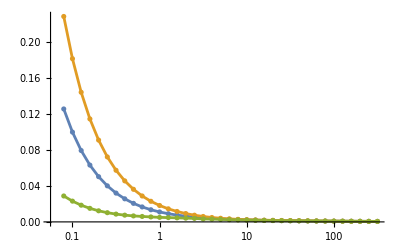

```mathematica
ListLogLinearPlot[{meanCepheidCDLTable,upperCepheidCDLTable,lowerCepheidCDLTable},Joined->True,Mesh->All,PlotRange->All]
```

##### Matchlight Plot

```mathematica
optimumσΔμCepheidPlot=ListPlot[{
Log10[meanCepheidCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperCepheidCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerCepheidCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[Lighter[color[1],.5],Opacity[.9]]},
PlotStyle->{
(*{AbsoluteThickness[3.5],Opacity[.5],color[1]},
{AbsoluteThickness[3.5],Opacity[.5],color[2]}*)None
},
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\text{Cepheid Calibration}",Magnification->1.35],-4Degree]],Scaled[{.2,0.44}]]
}]
```

-Graphics-

##### Observing just the brightest Type II SN

```mathematica
brightestSNTypeIITab=Table[Min[snPopulationTrialsTypeII[[i]]],{i,1,Length[snPopulationTrialsTypeII]}]
```

{13.3745,13.7985,10.835,12.3626,11.1931,13.7939,12.4415,14.3795,10.4972,11.2399,12.0699,12.9111,10.7097,12.1738,13.406,13.1674,11.5338,12.9138,11.6077,13.8984,10.2363,13.7939,13.8409,13.3291,11.1716}

```mathematica
observationTimeOfBrightestTypeIISNTab=Table[{brightestSNTypeIITab[[i]],tPlateauTypeII},{i,1,Length[brightestSNTypeIITab]}]
```

{{13.3745,540},{13.7985,540},{10.835,540},{12.3626,540},{11.1931,540},{13.7939,540},{12.4415,540},{14.3795,540},{10.4972,540},{11.2399,540},{12.0699,540},{12.9111,540},{10.7097,540},{12.1738,540},{13.406,540},{13.1674,540},{11.5338,540},{12.9138,540},{11.6077,540},{13.8984,540},{10.2363,540},{13.7939,540},{13.8409,540},{13.3291,540},{11.1716,540}}

```mathematica
σμCepheids[{observationTimeOfBrightestTypeIISNTab[[1]]},1]
```

0.0240762

```mathematica
matchlightCepheidCDLSingleTypeIISN=(
Table[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramTabSNRCepheidsSingleTypeIISN=Table[σμCepheids[{observationTimeOfBrightestTypeIISNTab[[i]]},snrEnhancementIterator],{i,1,numTrials}];
{snrEnhancementIterator,{Mean[histogramTabSNRCepheidsSingleTypeIISN],Quantile[histogramTabSNRCepheidsSingleTypeIISN,{oneσLowerQuantile,oneσUpperQuantile}](*StandardDeviation[histogramTabSNRCepheids]*)}},
{i,1,Length[snrEnhancementTab]}]
)
```

{{0.0794328,{0.21088,{0.0290234,0.438186}}},{0.1,{0.167592,{0.0232534,0.348077}}},{0.125893,{0.133227,{0.0187189,0.276504}}},{0.158489,{0.105955,{0.015176,0.219656}}},{0.199526,{0.0843216,{0.0124315,0.174505}}},{0.251189,{0.0671719,{0.0103313,0.138648}}},{0.316228,{0.0535884,{0.00875054,0.110174}}},{0.398107,{0.0428417,{0.00758549,0.0875668}}},{0.501187,{0.0343518,{0.00674768,0.069623}}},{0.630957,{0.0276569,{0.0061607,0.0553869}}},{0.794328,{0.0223895,{0.00575965,0.0441001}}},{1.,{0.0182568,{0.00549156,0.0351614}}},{1.25893,{0.015026,{0.00531545,0.0280944}}},{1.58489,{0.0125119,{0.00520126,0.0225219}}},{1.99526,{0.0105671,{0.00512791,0.0181458}}},{2.51189,{0.00907435,{0.00508108,0.0147303}}},{3.16228,{0.00793986,{0.00505131,0.0120885}}},{3.98107,{0.00708842,{0.00503243,0.0100712}}},{5.01187,{0.00645912,{0.00502049,0.00855708}}},{6.30957,{0.00600229,{0.00501294,0.00744494}}},{7.94328,{0.00567718,{0.00500817,0.00664817}}},{10.,{0.00545058,{0.00500515,0.00609206}}},{12.5893,{0.00529582,{0.00500325,0.0057134}}},{15.8489,{0.00519208,{0.00500205,0.00546099}}},{19.9526,{0.00512365,{0.0050013,0.00529554}}},{25.1189,{0.00507909,{0.00500082,0.00518843}}},{31.6228,{0.00505035,{0.00500052,0.0051197}}},{39.8107,{0.00503196,{0.00500033,0.00507585}}},{50.1187,{0.00502024,{0.00500021,0.00504799}}},{63.0957,{0.0050128,{0.00500013,0.00503034}}},{79.4328,{0.00500809,{0.00500008,0.00501916}}},{100.,{0.00500511,{0.00500005,0.0050121}}},{125.893,{0.00500323,{0.00500003,0.00500764}}},{158.489,{0.00500204,{0.00500002,0.00500482}}},{199.526,{0.00500129,{0.00500001,0.00500304}}},{251.189,{0.00500081,{0.00500001,0.00500192}}},{316.228,{0.00500051,{0.00500001,0.00500121}}}}

```mathematica
meanCepheidCDLSingleTypeIISNTable=Table[{matchlightCepheidCDLSingleTypeIISN[[i,1]],matchlightCepheidCDLSingleTypeIISN[[i,2,1]]},{i,1,Length[matchlightCepheidCDLSingleTypeIISN]}]
```

{{0.0794328,0.21088},{0.1,0.167592},{0.125893,0.133227},{0.158489,0.105955},{0.199526,0.0843216},{0.251189,0.0671719},{0.316228,0.0535884},{0.398107,0.0428417},{0.501187,0.0343518},{0.630957,0.0276569},{0.794328,0.0223895},{1.,0.0182568},{1.25893,0.015026},{1.58489,0.0125119},{1.99526,0.0105671},{2.51189,0.00907435},{3.16228,0.00793986},{3.98107,0.00708842},{5.01187,0.00645912},{6.30957,0.00600229},{7.94328,0.00567718},{10.,0.00545058},{12.5893,0.00529582},{15.8489,0.00519208},{19.9526,0.00512365},{25.1189,0.00507909},{31.6228,0.00505035},{39.8107,0.00503196},{50.1187,0.00502024},{63.0957,0.0050128},{79.4328,0.00500809},{100.,0.00500511},{125.893,0.00500323},{158.489,0.00500204},{199.526,0.00500129},{251.189,0.00500081},{316.228,0.00500051}}

```mathematica
upperCepheidCDLSingleTypeIISNTable=Table[{matchlightCepheidCDLSingleTypeIISN[[i,1]],matchlightCepheidCDLSingleTypeIISN[[i,2,2,2]]},{i,1,Length[matchlightCepheidCDLSingleTypeIISN]}]

lowerCepheidCDLSingleTypeIISNTable=Table[{matchlightCepheidCDLSingleTypeIISN[[i,1]],matchlightCepheidCDLSingleTypeIISN[[i,2,2,1]]},{i,1,Length[matchlightCepheidCDLSingleTypeIISN]}]
```

{{0.0794328,0.438186},{0.1,0.348077},{0.125893,0.276504},{0.158489,0.219656},{0.199526,0.174505},{0.251189,0.138648},{0.316228,0.110174},{0.398107,0.0875668},{0.501187,0.069623},{0.630957,0.0553869},{0.794328,0.0441001},{1.,0.0351614},{1.25893,0.0280944},{1.58489,0.0225219},{1.99526,0.0181458},{2.51189,0.0147303},{3.16228,0.0120885},{3.98107,0.0100712},{5.01187,0.00855708},{6.30957,0.00744494},{7.94328,0.00664817},{10.,0.00609206},{12.5893,0.0057134},{15.8489,0.00546099},{19.9526,0.00529554},{25.1189,0.00518843},{31.6228,0.0051197},{39.8107,0.00507585},{50.1187,0.00504799},{63.0957,0.00503034},{79.4328,0.00501916},{100.,0.0050121},{125.893,0.00500764},{158.489,0.00500482},{199.526,0.00500304},{251.189,0.00500192},{316.228,0.00500121}}

{{0.0794328,0.0290234},{0.1,0.0232534},{0.125893,0.0187189},{0.158489,0.015176},{0.199526,0.0124315},{0.251189,0.0103313},{0.316228,0.00875054},{0.398107,0.00758549},{0.501187,0.00674768},{0.630957,0.0061607},{0.794328,0.00575965},{1.,0.00549156},{1.25893,0.00531545},{1.58489,0.00520126},{1.99526,0.00512791},{2.51189,0.00508108},{3.16228,0.00505131},{3.98107,0.00503243},{5.01187,0.00502049},{6.30957,0.00501294},{7.94328,0.00500817},{10.,0.00500515},{12.5893,0.00500325},{15.8489,0.00500205},{19.9526,0.0050013},{25.1189,0.00500082},{31.6228,0.00500052},{39.8107,0.00500033},{50.1187,0.00500021},{63.0957,0.00500013},{79.4328,0.00500008},{100.,0.00500005},{125.893,0.00500003},{158.489,0.00500002},{199.526,0.00500001},{251.189,0.00500001},{316.228,0.00500001}}

```mathematica
optimumσΔμCepheidSingleTypeIISNPlot=ListPlot[{
Log10[meanCepheidCDLSingleTypeIISNTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperCepheidCDLSingleTypeIISNTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerCepheidCDLSingleTypeIISNTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[Lighter[color[1],.5],Opacity[.25]]},
PlotStyle->{
(*{AbsoluteThickness[3.5],Opacity[.5],color[1]},
{AbsoluteThickness[3.5],Opacity[.5],color[2]}*)None
},
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\text{Cepheid Calibration}",Magnification->1.35],-4Degree]],Scaled[{.2,0.44}]]
}]
```

-Graphics-

### σμ Optimization for Type Ia SN(with max observation cutoff)

```mathematica
σCalibratorTypeIa[m_]:=0.13*Log[10]/5;
```

```mathematica
numTrials=10(*50*)(*500*);
numYrs=5;
snPopulationTrialsTypeIa=Table[Sort[
Flatten[Table[
snYearRealization[m0CDF,18,b0CDF,typeIaFraction]
,{yrs,1,numYrs}]]
],{i,1,numTrials}];
```

```mathematica
tiLangrangeMultiplierTypeIa[inputSNList_,tTotalObservationhr_,snrEnhancement_]:=(
snPopList=inputSNList;
sum1UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σCalibratorTypeIa[snPopList[[i]]])^2 t0hr,{i,1,Length[snPopList]}];
sum2UncertaintyRatio=Sum[(σDoverDt0[snPopList[[i]],snrEnhancement]/σCalibratorTypeIa[snPopList[[i]]]^2),{i,1,Length[snPopList]}];
tiIdealTypeIaTab=Table[
mi=snPopList[[i]];
ti=(tTotalObservationhr+sum1UncertaintyRatio)*(σDoverDt0[mi,snrEnhancement]/σCalibratorTypeIa[mi]^2)/sum2UncertaintyRatio-(σDoverDt0[mi,snrEnhancement]/σCalibratorTypeIa[mi])^2*t0hr;
{mi,ti},{i,1,Length[snPopList]}]
)
```

```mathematica
tiIdealTypeIaList[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0,numOftPlateauSN_:0,fiducialNumSN_:-1]:=(

If[trialNum==0,
snPop=Sort[snYearRealization[m0CDF,18,b0CDF,typeIaFraction]],
snPop=snPopulationTrialsTypeIa[[trialNum]][[numOftPlateauSN+1;;fiducialNumSN]]];

tiTimesPositiveDefinite=False;
snListLength=Length[snPop];
reducedSNPopList=snPop;


While[
tiTimesPositiveDefinite===False,
newtiTab=tiLangrangeMultiplierTypeIa[reducedSNPopList,tTotalObservationhr,snrEnhancement];
observationTimeoDimmestSN=newtiTab[[-1]][[2]];
If[observationTimeoDimmestSN<=0,reducedSNPopList=Drop[reducedSNPopList,-1];,tiTimesPositiveDefinite=True];
];
newtiTab
)
```

```mathematica
σμTypeIa[inputSNList_,snrEnhancement_]:=(
snPopList=inputSNList;
σμIdealTypeIa=(Sum[1/((σDoverDt[snPopList[[i,1]],snrEnhancement,snPopList[[i,2]]])^2+σCalibratorTypeIa[snPopList[[i,1]]]^2),{i,1,Length[snPopList]}])^(-1/2)
)
```

```mathematica
tPlateauTypeIa=1*30*6;
numOftPlateauTypeIa=0;
```

```mathematica
redoIdealσμHistogramTypeIa[inputSNList_,snrEnhancement_,trialNum_]:=Module[{snPopList=inputSNList},
(
(*tObsOfBrightestSN=snPopList[[1,2]];*)
tObsOfBrightestTypeIa=Max[snPopList[[;;,2]]];
totalObsTimeForOptimizationTypeIa=Sum[snPopList[[i,2]],{i,1,Length[snPopList]}];
numOfFiducialTypeIa=Length[snPopList];
numOftPlateauTypeIa=0;
updatedtiIdealTypeIaList=snPopList;
While[tObsOfBrightestTypeIa>tPlateauTypeIa,
numOftPlateauTypeIa=numOftPlateauTypeIa+1;
updatedtiIdealTypeIaList=tiIdealTypeIaList[totalObsTimeForOptimizationTypeIa-tPlateauTypeIa,snrEnhancement,trialNum,numOftPlateauTypeIa,numOfFiducialTypeIa+(*50*)75];
(*tObsOfBrightestSN=updatedtiIdealCepheidsList[[1,2]];*)
tObsOfBrightestTypeIa=Max[updatedtiIdealTypeIaList[[;;,2]]];
totalObsTimeForOptimizationTypeIa=Sum[updatedtiIdealTypeIaList[[i,2]],{i,1,Length[updatedtiIdealTypeIaList]}];
numOfFiducialSNTypeIa=Length[updatedtiIdealTypeIaList];
];
plateauTypeIaTab=Table[{snPopulationTrialsTypeIa[[trialNum,i]],tPlateauTypeIa},{i,1,numOftPlateauTypeIa}];
Join[plateauTypeIaTab,updatedtiIdealTypeIaList]
)]
```

```mathematica
idealσμHistogramTypeIa[tTotalObservationhr_?NumericQ,snrEnhancement_,trialNum_:0]:=(
Table[
(*idealSNPopulation=tiIdealTypeIaList[tTotalObservationhr,snrEnhancement,0];*)
idealSNPopulationIa=tiIdealTypeIaList[tTotalObservationhr,snrEnhancement,i];
idealSNPopulationIaPlateau=redoIdealσμHistogramTypeIa[idealSNPopulationIa,snrEnhancement,i];
σμTypeIa[idealSNPopulationIaPlateau,snrEnhancement],{i,1,numTrials}])
```

```mathematica
snrEnhancementTab=Table[10^logSNREnhancement,{logSNREnhancement,-1.1,2.5,.1}]
```

{0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228}

```mathematica
matchlightTypeIaCDL[tTotalObservationhr_?NumericQ]:=(
ParallelTable[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramTabSNRTypeIa=idealσμHistogramTypeIa[tTotalObservationhr,snrEnhancementIterator];
{snrEnhancementIterator,{Mean[histogramTabSNRTypeIa],Quantile[histogramTabSNRTypeIa,{oneσLowerQuantile,oneσUpperQuantile}](*StandardDeviation[histogramTabSNRTypeIa]*)}},
{i,1,Length[snrEnhancementTab]}]
)
```

```mathematica
matchlightTypeIaCDLTab=matchlightTypeIaCDL[365*6*numYrs]
```

{{0.0794328,{0.0369425,{0.0285787,0.0427637}}},{0.1,{0.0321095,{0.0256658,0.037446}}},{0.125893,{0.0280478,{0.023037,0.0330678}}},{0.158489,{0.0246004,{0.0206407,0.0290576}}},{0.199526,{0.0216541,{0.0184713,0.0254209}}},{0.251189,{0.0191285,{0.0165391,0.0221867}}},{0.316228,{0.0169646,{0.0148492,0.0193176}}},{0.398107,{0.0151175,{0.013395,0.0169423}}},{0.501187,{0.0135508,{0.0121612,0.0149851}}},{0.630957,{0.0122328,{0.0111272,0.0133318}}},{0.794328,{0.011134,{0.0102675,0.011977}}},{1.,{0.0101862,{0.00942227,0.0108733}}},{1.25893,{0.00922687,{0.00859247,0.00985157}}},{1.58489,{0.00842948,{0.00791133,0.00891919}}},{1.99526,{0.00770911,{0.00728354,0.00806902}}},{2.51189,{0.00704871,{0.00670101,0.00730731}}},{3.16228,{0.00644571,{0.00616405,0.00662318}}},{3.98107,{0.00589662,{0.0056736,0.00602257}}},{5.01187,{0.00539308,{0.00521652,0.00552328}}},{6.30957,{0.00493218,{0.00479302,0.00505986}}},{7.94328,{0.0045107,{0.00440273,0.00462824}}},{10.,{0.00412524,{0.00403622,0.00422759}}},{12.5893,{0.00377259,{0.00370404,0.00385706}}},{15.8489,{0.00344974,{0.00339827,0.00352359}}},{19.9526,{0.00315416,{0.00311557,0.00321564}}},{25.1189,{0.00288375,{0.00285343,0.00293538}}},{31.6228,{0.00263664,{0.00261084,0.00267874}}},{39.8107,{0.00241094,{0.00238791,0.00244369}}},{50.1187,{0.00220491,{0.00218428,0.00223088}}},{63.0957,{0.00201671,{0.00200073,0.00203782}}},{79.4328,{0.00184447,{0.00183247,0.00186187}}},{100.,{0.00168683,{0.00167774,0.00170067}}},{125.893,{0.00154267,{0.00153557,0.00155343}}},{158.489,{0.00141089,{0.00140506,0.00141927}}},{199.526,{0.00129125,{0.00128671,0.00129759}}},{251.189,{0.00118888,{0.00118547,0.0011935}}},{316.228,{0.00110766,{0.00110519,0.00111091}}}}

```mathematica
Export[NotebookDirectory[]<>"Data/matchlightTypeIaCDLTab.m",matchlightTypeIaCDLTab]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Data/matchlightTypeIaCDLTab.m

```mathematica
matchlightTypeIaCDLTab=Import[NotebookDirectory[]<>"Data/matchlightTypeIaCDLTab.m"]
```

{{0.0794328,{0.0369425,{0.0285787,0.0427637}}},{0.1,{0.0321095,{0.0256658,0.037446}}},{0.125893,{0.0280478,{0.023037,0.0330678}}},{0.158489,{0.0246004,{0.0206407,0.0290576}}},{0.199526,{0.0216541,{0.0184713,0.0254209}}},{0.251189,{0.0191285,{0.0165391,0.0221867}}},{0.316228,{0.0169646,{0.0148492,0.0193176}}},{0.398107,{0.0151175,{0.013395,0.0169423}}},{0.501187,{0.0135508,{0.0121612,0.0149851}}},{0.630957,{0.0122328,{0.0111272,0.0133318}}},{0.794328,{0.011134,{0.0102675,0.011977}}},{1.,{0.0101862,{0.00942227,0.0108733}}},{1.25893,{0.00922687,{0.00859247,0.00985157}}},{1.58489,{0.00842948,{0.00791133,0.00891919}}},{1.99526,{0.00770911,{0.00728354,0.00806902}}},{2.51189,{0.00704871,{0.00670101,0.00730731}}},{3.16228,{0.00644571,{0.00616405,0.00662318}}},{3.98107,{0.00589662,{0.0056736,0.00602257}}},{5.01187,{0.00539308,{0.00521652,0.00552328}}},{6.30957,{0.00493218,{0.00479302,0.00505986}}},{7.94328,{0.0045107,{0.00440273,0.00462824}}},{10.,{0.00412524,{0.00403622,0.00422759}}},{12.5893,{0.00377259,{0.00370404,0.00385706}}},{15.8489,{0.00344974,{0.00339827,0.00352359}}},{19.9526,{0.00315416,{0.00311557,0.00321564}}},{25.1189,{0.00288375,{0.00285343,0.00293538}}},{31.6228,{0.00263664,{0.00261084,0.00267874}}},{39.8107,{0.00241094,{0.00238791,0.00244369}}},{50.1187,{0.00220491,{0.00218428,0.00223088}}},{63.0957,{0.00201671,{0.00200073,0.00203782}}},{79.4328,{0.00184447,{0.00183247,0.00186187}}},{100.,{0.00168683,{0.00167774,0.00170067}}},{125.893,{0.00154267,{0.00153557,0.00155343}}},{158.489,{0.00141089,{0.00140506,0.00141927}}},{199.526,{0.00129125,{0.00128671,0.00129759}}},{251.189,{0.00118888,{0.00118547,0.0011935}}},{316.228,{0.00110766,{0.00110519,0.00111091}}}}

```mathematica
meanTypeIaCDLTable=Table[{matchlightTypeIaCDLTab[[i,1]],matchlightTypeIaCDLTab[[i,2,1]]},{i,1,Length[matchlightTypeIaCDLTab]}]
```

{{0.0794328,0.0369425},{0.1,0.0321095},{0.125893,0.0280478},{0.158489,0.0246004},{0.199526,0.0216541},{0.251189,0.0191285},{0.316228,0.0169646},{0.398107,0.0151175},{0.501187,0.0135508},{0.630957,0.0122328},{0.794328,0.011134},{1.,0.0101862},{1.25893,0.00922687},{1.58489,0.00842948},{1.99526,0.00770911},{2.51189,0.00704871},{3.16228,0.00644571},{3.98107,0.00589662},{5.01187,0.00539308},{6.30957,0.00493218},{7.94328,0.0045107},{10.,0.00412524},{12.5893,0.00377259},{15.8489,0.00344974},{19.9526,0.00315416},{25.1189,0.00288375},{31.6228,0.00263664},{39.8107,0.00241094},{50.1187,0.00220491},{63.0957,0.00201671},{79.4328,0.00184447},{100.,0.00168683},{125.893,0.00154267},{158.489,0.00141089},{199.526,0.00129125},{251.189,0.00118888},{316.228,0.00110766}}

```mathematica
upperTypeIaCDLTable=Table[{matchlightTypeIaCDLTab[[i,1]],matchlightTypeIaCDLTab[[i,2,2,2]]},{i,1,Length[matchlightTypeIaCDLTab]}]

lowerTypeIaCDLTable=Table[{matchlightTypeIaCDLTab[[i,1]],matchlightTypeIaCDLTab[[i,2,2,1]]},{i,1,Length[matchlightTypeIaCDLTab]}]
```

{{0.0794328,0.0427637},{0.1,0.037446},{0.125893,0.0330678},{0.158489,0.0290576},{0.199526,0.0254209},{0.251189,0.0221867},{0.316228,0.0193176},{0.398107,0.0169423},{0.501187,0.0149851},{0.630957,0.0133318},{0.794328,0.011977},{1.,0.0108733},{1.25893,0.00985157},{1.58489,0.00891919},{1.99526,0.00806902},{2.51189,0.00730731},{3.16228,0.00662318},{3.98107,0.00602257},{5.01187,0.00552328},{6.30957,0.00505986},{7.94328,0.00462824},{10.,0.00422759},{12.5893,0.00385706},{15.8489,0.00352359},{19.9526,0.00321564},{25.1189,0.00293538},{31.6228,0.00267874},{39.8107,0.00244369},{50.1187,0.00223088},{63.0957,0.00203782},{79.4328,0.00186187},{100.,0.00170067},{125.893,0.00155343},{158.489,0.00141927},{199.526,0.00129759},{251.189,0.0011935},{316.228,0.00111091}}

{{0.0794328,0.0285787},{0.1,0.0256658},{0.125893,0.023037},{0.158489,0.0206407},{0.199526,0.0184713},{0.251189,0.0165391},{0.316228,0.0148492},{0.398107,0.013395},{0.501187,0.0121612},{0.630957,0.0111272},{0.794328,0.0102675},{1.,0.00942227},{1.25893,0.00859247},{1.58489,0.00791133},{1.99526,0.00728354},{2.51189,0.00670101},{3.16228,0.00616405},{3.98107,0.0056736},{5.01187,0.00521652},{6.30957,0.00479302},{7.94328,0.00440273},{10.,0.00403622},{12.5893,0.00370404},{15.8489,0.00339827},{19.9526,0.00311557},{25.1189,0.00285343},{31.6228,0.00261084},{39.8107,0.00238791},{50.1187,0.00218428},{63.0957,0.00200073},{79.4328,0.00183247},{100.,0.00167774},{125.893,0.00153557},{158.489,0.00140506},{199.526,0.00128671},{251.189,0.00118547},{316.228,0.00110519}}

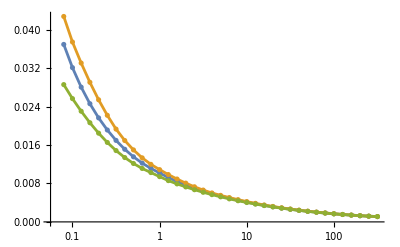

```mathematica
ListLogLinearPlot[{meanTypeIaCDLTable,upperTypeIaCDLTable,lowerTypeIaCDLTable},Joined->True,Mesh->All,PlotRange->All]
```

##### Matchlight Plot

```mathematica
optimumσΔμTypeIaPlot=ListPlot[{
Log10[meanTypeIaCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperTypeIaCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerTypeIaCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[color[2],Opacity[.5]]},
PlotStyle->{
(*{AbsoluteThickness[3.5],Opacity[.5],color[1]},
{AbsoluteThickness[3.5],Opacity[.5],color[2]}*)None
}
,
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[1*10^0]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{\\mu}
",Magnification->1.5],None},
{MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5],None(*MaTeX["\\text{Max SN Type-II Observational Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{SN Ia Calibration}",Magnification->1.35],-5Degree]],Scaled[{.2,0.38}]]
}]
```

-Graphics-

```mathematica
(*Export[NotebookDirectory[]<>"optimumTypeIaigmaMuPlot.pdf",optimumσΔμTypeIaPlot]*)
```

##### Observing just the brightest Type Ia SN

```mathematica
brightestSNTypeIaTab=Table[Min[snPopulationTrialsTypeIa[[i]]],{i,1,Length[snPopulationTrialsTypeIa]}]
```

{10.7734,9.09968,10.5584,11.426,10.0328,9.88578,10.0281,9.86623,9.46314,10.8326}

```mathematica
observationTimeOfBrightestTypeIaSNTab=Table[{brightestSNTypeIaTab[[i]],tPlateauTypeIa},{i,1,Length[brightestSNTypeIaTab]}]
```

{{10.7734,180},{9.09968,180},{10.5584,180},{11.426,180},{10.0328,180},{9.88578,180},{10.0281,180},{9.86623,180},{9.46314,180},{10.8326,180}}

```mathematica
σμTypeIa[{observationTimeOfBrightestTypeIaSNTab[[1]]},1]
```

0.0599825

```mathematica
matchlightCepheidCDLSingleTypeIaSN=(
Table[
snrEnhancementIterator=snrEnhancementTab[[i]];
histogramTabSNRCepheidsSingleTypeIaSN=Table[σμTypeIa[{observationTimeOfBrightestTypeIaSNTab[[i]]},snrEnhancementIterator],{i,1,numTrials}];
{snrEnhancementIterator,{Mean[histogramTabSNRCepheidsSingleTypeIaSN],Quantile[histogramTabSNRCepheidsSingleTypeIaSN,{oneσLowerQuantile,oneσUpperQuantile}](*StandardDeviation[histogramTabSNRCepheids]*)}},
{i,1,Length[snrEnhancementTab]}]
)
```

{{0.0794328,{0.0706399,{0.0614817,0.0776231}}},{0.1,{0.0670505,{0.0608909,0.071585}}},{0.125893,{0.064594,{0.0605151,0.0674979}}},{0.158489,{0.0629427,{0.0602768,0.0647866}}},{0.199526,{0.0618503,{0.060126,0.0630158}}},{0.251189,{0.0611371,{0.0600306,0.0618725}}},{0.316228,{0.0606765,{0.0599704,0.0611401}}},{0.398107,{0.0603811,{0.0599323,0.0606735}}},{0.501187,{0.0601928,{0.0599083,0.0603772}}},{0.630957,{0.0600732,{0.0598931,0.0601895}}},{0.794328,{0.0599974,{0.0598836,0.0600708}}},{1.,{0.0599495,{0.0598775,0.0599957}}},{1.25893,{0.0599191,{0.0598737,0.0599483}}},{1.58489,{0.0599,{0.0598713,0.0599184}}},{1.99526,{0.0598879,{0.0598698,0.0598995}}},{2.51189,{0.0598803,{0.0598688,0.0598876}}},{3.16228,{0.0598755,{0.0598682,0.0598801}}},{3.98107,{0.0598724,{0.0598679,0.0598753}}},{5.01187,{0.0598705,{0.0598676,0.0598723}}},{6.30957,{0.0598693,{0.0598675,0.0598704}}},{7.94328,{0.0598685,{0.0598674,0.0598693}}},{10.,{0.059868,{0.0598673,0.0598685}}},{12.5893,{0.0598677,{0.0598673,0.059868}}},{15.8489,{0.0598675,{0.0598673,0.0598677}}},{19.9526,{0.0598674,{0.0598672,0.0598675}}},{25.1189,{0.0598673,{0.0598672,0.0598674}}},{31.6228,{0.0598673,{0.0598672,0.0598673}}},{39.8107,{0.0598673,{0.0598672,0.0598673}}},{50.1187,{0.0598672,{0.0598672,0.0598673}}},{63.0957,{0.0598672,{0.0598672,0.0598672}}},{79.4328,{0.0598672,{0.0598672,0.0598672}}},{100.,{0.0598672,{0.0598672,0.0598672}}},{125.893,{0.0598672,{0.0598672,0.0598672}}},{158.489,{0.0598672,{0.0598672,0.0598672}}},{199.526,{0.0598672,{0.0598672,0.0598672}}},{251.189,{0.0598672,{0.0598672,0.0598672}}},{316.228,{0.0598672,{0.0598672,0.0598672}}}}

```mathematica
meanCepheidCDLSingleTypeIaSNTable=Table[{matchlightCepheidCDLSingleTypeIaSN[[i,1]],matchlightCepheidCDLSingleTypeIaSN[[i,2,1]]},{i,1,Length[matchlightCepheidCDLSingleTypeIaSN]}]
```

{{0.0794328,0.0706399},{0.1,0.0670505},{0.125893,0.064594},{0.158489,0.0629427},{0.199526,0.0618503},{0.251189,0.0611371},{0.316228,0.0606765},{0.398107,0.0603811},{0.501187,0.0601928},{0.630957,0.0600732},{0.794328,0.0599974},{1.,0.0599495},{1.25893,0.0599191},{1.58489,0.0599},{1.99526,0.0598879},{2.51189,0.0598803},{3.16228,0.0598755},{3.98107,0.0598724},{5.01187,0.0598705},{6.30957,0.0598693},{7.94328,0.0598685},{10.,0.059868},{12.5893,0.0598677},{15.8489,0.0598675},{19.9526,0.0598674},{25.1189,0.0598673},{31.6228,0.0598673},{39.8107,0.0598673},{50.1187,0.0598672},{63.0957,0.0598672},{79.4328,0.0598672},{100.,0.0598672},{125.893,0.0598672},{158.489,0.0598672},{199.526,0.0598672},{251.189,0.0598672},{316.228,0.0598672}}

```mathematica
upperCepheidCDLSingleTypeIaSNTable=Table[{matchlightCepheidCDLSingleTypeIaSN[[i,1]],matchlightCepheidCDLSingleTypeIaSN[[i,2,2,2]]},{i,1,Length[matchlightCepheidCDLSingleTypeIaSN]}]

lowerCepheidCDLSingleTypeIaSNTable=Table[{matchlightCepheidCDLSingleTypeIaSN[[i,1]],matchlightCepheidCDLSingleTypeIaSN[[i,2,2,1]]},{i,1,Length[matchlightCepheidCDLSingleTypeIaSN]}]
```

{{0.0794328,0.0776231},{0.1,0.071585},{0.125893,0.0674979},{0.158489,0.0647866},{0.199526,0.0630158},{0.251189,0.0618725},{0.316228,0.0611401},{0.398107,0.0606735},{0.501187,0.0603772},{0.630957,0.0601895},{0.794328,0.0600708},{1.,0.0599957},{1.25893,0.0599483},{1.58489,0.0599184},{1.99526,0.0598995},{2.51189,0.0598876},{3.16228,0.0598801},{3.98107,0.0598753},{5.01187,0.0598723},{6.30957,0.0598704},{7.94328,0.0598693},{10.,0.0598685},{12.5893,0.059868},{15.8489,0.0598677},{19.9526,0.0598675},{25.1189,0.0598674},{31.6228,0.0598673},{39.8107,0.0598673},{50.1187,0.0598673},{63.0957,0.0598672},{79.4328,0.0598672},{100.,0.0598672},{125.893,0.0598672},{158.489,0.0598672},{199.526,0.0598672},{251.189,0.0598672},{316.228,0.0598672}}

{{0.0794328,0.0614817},{0.1,0.0608909},{0.125893,0.0605151},{0.158489,0.0602768},{0.199526,0.060126},{0.251189,0.0600306},{0.316228,0.0599704},{0.398107,0.0599323},{0.501187,0.0599083},{0.630957,0.0598931},{0.794328,0.0598836},{1.,0.0598775},{1.25893,0.0598737},{1.58489,0.0598713},{1.99526,0.0598698},{2.51189,0.0598688},{3.16228,0.0598682},{3.98107,0.0598679},{5.01187,0.0598676},{6.30957,0.0598675},{7.94328,0.0598674},{10.,0.0598673},{12.5893,0.0598673},{15.8489,0.0598673},{19.9526,0.0598672},{25.1189,0.0598672},{31.6228,0.0598672},{39.8107,0.0598672},{50.1187,0.0598672},{63.0957,0.0598672},{79.4328,0.0598672},{100.,0.0598672},{125.893,0.0598672},{158.489,0.0598672},{199.526,0.0598672},{251.189,0.0598672},{316.228,0.0598672}}

```mathematica
optimumσΔμCepheidSingleTypeIaSNPlot=ListPlot[{
Log10[meanCepheidCDLSingleTypeIaSNTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[upperCepheidCDLSingleTypeIaSNTable/.{x_,y_}->{x*figureOfMeritStnd,y}],
Log10[lowerCepheidCDLSingleTypeIaSNTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,
(*Mesh->All,*)
PlotStyle->{
{AbsoluteThickness[.5],Opacity[1],Lighter[color[2],.7]},
{AbsoluteThickness[.5],Opacity[1],Lighter[color[2],.7]},
{AbsoluteThickness[.5],Opacity[1],Lighter[color[2],.7]}
}
,(*PlotStyle->None,*)
Filling->{2->{3}},
FillingStyle->{Directive[Lighter[color[2],.7],Opacity[1]]},
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[1*10^0]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\sigma_{\\mu}
",Magnification->1.5],None},
{MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5],None(*MaTeX["\\text{Max SN Type-II Observational Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{SN Ia Calibration}",Magnification->1.35],-5Degree]],Scaled[{.2,0.38}]]
}]
```

-Graphics-

### SH0ES Uncertainties

```mathematica
σSH0ESCDL1=0.7*10^-2;
σSH0ESCDL3=0.4*10^-2;
σSH0ESCDL2=√(0.4^2+0.9^2+0.3^2)*10^-2;
σSH0ESCDLSystematics=0.3*10^-2;
```

```mathematica
σSH0ESCDLStatistics=√(σSH0ESCDL1^2+σSH0ESCDL2^2+σSH0ESCDL3^2)
```

0.0130767

```mathematica
σSH0ESCDLTotal=√(σSH0ESCDLStatistics^2+σSH0ESCDLSystematics^2)
```

0.0134164

```mathematica
σPlanckSH0ESDiscrepancy=7*10^-2;
```

```mathematica
√(σSH0ESCDL2^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2)*100
```

1.14455

```mathematica
SH0ESUncertaintyPlot=Plot[{
Log10[σSH0ESCDL1],
Log10[σSH0ESCDL2],
Log10[σSH0ESCDL3],
Log10[σPlanckSH0ESDiscrepancy],
Log10[σSH0ESCDLSystematics]
},{x,1,10},
PlotStyle->{
{AbsoluteThickness[2],Opacity[.85/3],color[1]},
{AbsoluteThickness[2],Opacity[.85/3],color[2]},
{AbsoluteThickness[2],Opacity[.85/3],color[3]},
{AbsoluteThickness[2],Opacity[.85],color[4],Dashed},
{AbsoluteThickness[2],Opacity[.85/3],color[5]}
},
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5],None(*MaTeX["\\text{Max SN Type-II Observational Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->425*.805,AspectRatio->1/(.75*GoldenRatio),
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{SH0ES}",Magnification->1.35],0Degree]],Scaled[{.2,0.38}]]
}]

SH0ESLinePlotUncertaintyPlot=Plot[{
Log10[σPlanckSH0ESDiscrepancy],
},{x,1,10},
PlotStyle->{
{AbsoluteThickness[2],Opacity[.85],color[4],Dashed},
},
Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5],None(*MaTeX["\\text{Max SN Type-II Observational Distance [Mpc]}",Magnification->1.5]*)}},ImageSize->425*.805,AspectRatio->1/(.75*GoldenRatio),
ImagePadding->{{80,20},{70,70}},
Epilog->{
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\text{SH0ES}",Magnification->1.35],0Degree]],Scaled[{.2,0.38}]]
}]
```

-Graphics-

-Graphics-

### Combined CDL Calibration Plot

```mathematica
combinedCDLPlot=Show[SH0ESUncertaintyPlot,optimumσΔμCepheidPlot,optimumσΔμTypeIaPlot,optimumσΔμCepheidSingleTypeIISNPlot,optimumσΔμCepheidSingleTypeIaSNPlot,SH0ESLinePlotUncertaintyPlot,
Epilog->{
(*Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\sigma_{\\rm rung \\, 1,EEM}",Magnification->1.45],-35Degree]],Scaled[{.15-.02+.1+.05-.075,0.48+.05-.05+.075-.125}]],*)
Inset[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\sigma_{\\rm rung \\, 1,EEM}",Magnification->1.45],-28.5 Degree]],Scaled[{.15-.02+.1+.05-.04+.1+.15,0.48+.05-.05+.075-.165+.02-.05-.075+.03-.005}]],
(*Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\sigma_{\\rm rung \\, 2,EEM}",Magnification->1.45],-19Degree]],Scaled[{.225+.055+.075,0.715+.01-.04-.15-.075}]],*)
Inset[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\sigma_{\\rm rung \\, 2,EEM}",Magnification->1.45],-27.5Degree]],Scaled[{.225+.055+.075-.15-.02+.125-.025,0.715+.01-.04-.2+.033+.025-.1+.075+.025}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[1],.3]]@MaTeX["\\sigma_{\\rm rung \\, 1,SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.775+.028,.405+.0075}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[2],.3]]@MaTeX["\\sigma_{\\rm rung \\, 2,SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.775+.028,.475+.01}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[3],.3]]@MaTeX["\\sigma_{\\rm rung \\, 3,SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.775+.028,.31}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[5],.3]]@MaTeX["\\sigma_{\\rm sys, \\, SH0ES}",Magnification->1.35],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.775+.055,.183+.062}]],
Inset[Framed[Style[Rotate[changeStyle[Darker[color[4],.3]]@MaTeX["({H_0}_{\\,\\rm CMB} - {H_0}_{\\, \\rm SH0ES})/{H_0}_{\\, \\rm SH0ES}",Magnification->1.3],0Degree]],Background->Directive[White,Opacity[0]],FrameStyle->None,FrameMargins->{{None,None},{-5,-5}}],Scaled[{.56,.85}]]}]
```

-Graphics-

##### Large Ticks

```mathematica
(*highLightedTicks={500,2.4*10^4,1.2*10^6};*)
highLightedTicks={lowMatchlightPaper,highMatchlightPaper}
```

{1250,50000}

```mathematica
highlightedFrameTicks=Table[{Log10[highLightedTicks[[i]]],.1},{i,1,Length[highLightedTicks]}]
```

{{Log[1250]/Log[10],0.1},{Log[50000]/Log[10],0.1}}

```mathematica
highLightedTicksTabLightBlue={
{Log10[lowMatchlightPaper],"", {5*0.0125,0}}}

highLightedTicksTabMidBlue={
{Log10[highMatchlightPaper],"", {5*0.0125,0}}}
```

{{Log[1250]/Log[10],,{0.0625,0}}}

{{Log[50000]/Log[10],,{0.0625,0}}}

```mathematica
lightBlueTicksPlot=Plot[{Log10[σSH0ESCDL1],Log10[σSH0ESCDL2],Log10[σSH0ESCDL3],Log10[σPlanckSH0ESDiscrepancy],Log10[σSH0ESCDLSystematics]},{x,1,10},PlotStyle->None,Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{highlightedFrameTicks,Automatic},{highLightedTicksTabLightBlue,None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Darker[xgfsnormal12TabColors[[10]],0],AbsoluteThickness[2.5]}],ImageSize->425*.805,AspectRatio->1/(.75*GoldenRatio),ImagePadding->{{80,20},{70,70}}]

midBlueTicksPlot=Plot[{Log10[σSH0ESCDL1],Log10[σSH0ESCDL2],Log10[σSH0ESCDL3],Log10[σPlanckSH0ESDiscrepancy],Log10[σSH0ESCDLSystematics]},{x,1,10},PlotStyle->None,Frame->True,Axes->False,PlotRange->{{Log10[10^2],Log10[10^5]},{-3,Log10[2*10^-1]}},
FrameTicks->{{highlightedFrameTicks,Automatic},{highLightedTicksTabMidBlue,None}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5],Opacity[1]}],FrameTicksStyle->Directive[{Darker[xgfsnormal12TabColors[[3]],0],AbsoluteThickness[2.5]}],ImageSize->425*.805,AspectRatio->1/(.75*GoldenRatio),ImagePadding->{{80,20},{70,70}}]
```

-Graphics-

-Graphics-

```mathematica
totalCombineCDLPlot=Overlay[{combinedCDLPlot,midBlueTicksPlot,lightBlueTicksPlot}]
```

-Graphics--Graphics--Graphics-

```mathematica
gridDistanceCDLPlot=Grid[{{distancePrecisionComparisonPlot,totalCombineCDLPlot(*combinedCDLPlot*)}}]
```

-Graphics- | -Graphics--Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"Figures/gridDistanceCDLPlot.pdf",gridDistanceCDLPlot]
```

/Users/david/Documents/Projects/EPIC Hubble/Github Code/Figures/gridDistanceCDLPlot.pdf

### Sigma Uncertainty to Resolve Hubble Tension

##### Rung 1

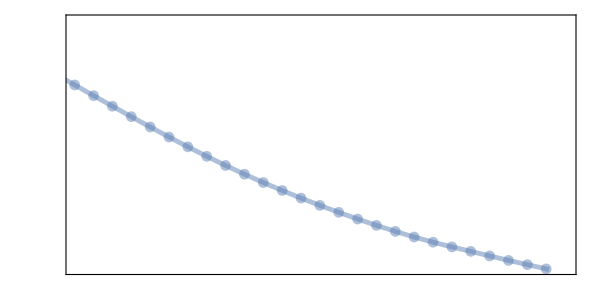

```mathematica
ListPlot[{
Log10[meanCepheidCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[Lighter[color[1],.5],Opacity[.9]]},
PlotStyle->{
{AbsoluteThickness[3.5],Opacity[.5],color[1]},
{AbsoluteThickness[3.5],Opacity[.5],color[2]}
},
Frame->True,Axes->False,PlotRange->{{2.4,Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

```mathematica
logmeanCepheidCDLInterp=Interpolation[Log10[meanCepheidCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]]
```

InterpolatingFunction[…]

```mathematica
meanCepheidCDLInterp[matchlight_]:=Evaluate[Power[10,logmeanCepheidCDLInterp[Log10[matchlight]]]]
```

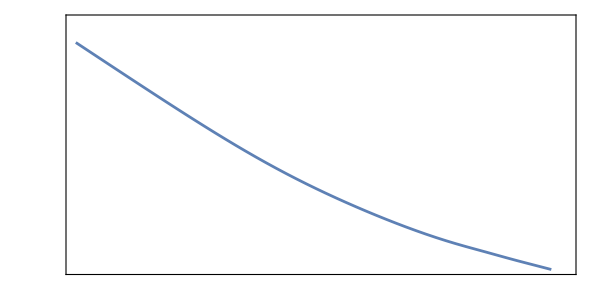

```mathematica
Plot[Log10[meanCepheidCDLInterp[10^logmatchlight]],{logmatchlight,2,5},Frame->True,Axes->False,PlotRange->{{2,Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

```mathematica
n2Sigma=2;
n3Sigma=3;
```

```mathematica
matchlight2SigmaSolutionCDLRung1=First[findAllRoots[meanCepheidCDLInterp[matchlight]^2+σSH0ESCDL2^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2-σPlanckSH0ESDiscrepancy^2/n2Sigma^2,{matchlight,10^2,10^5}]]
```

380.34

```mathematica
meanCepheidCDLInterp[500]
```

0.0254039

```mathematica
matchlight3SigmaSolutionCDLRung1=First[findAllRoots[meanCepheidCDLInterp[matchlight]^2+σSH0ESCDL2^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2-σPlanckSH0ESDiscrepancy^2/n3Sigma^2,{matchlight,10^2,10^5}]]
```

632.362

```mathematica
meanCepheidCDLInterp[800]
```

0.0163488

```mathematica
√(meanCepheidCDLInterp[1250]^2+σSH0ESCDL2^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2)
```

0.0158735

```mathematica
√(meanCepheidCDLInterp[50000]^2+σSH0ESCDL2^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2)
```

0.0115091

```mathematica
(*Export[NotebookDirectory[]<>"optimumCepheidSigmaMuPlot.pdf",optimumσΔμCepheidPlot]*)
```

##### Rung 2

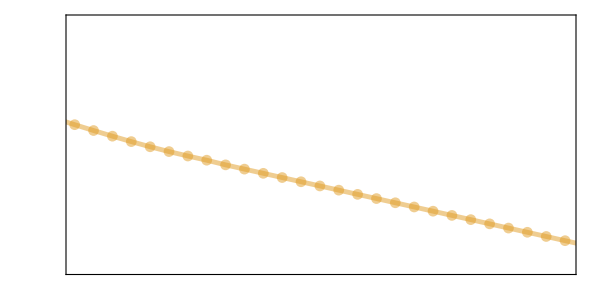

```mathematica
ListPlot[{
Log10[meanTypeIaCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]
},
Joined->True,Mesh->All,
Filling->{2->{3}},
FillingStyle->{Directive[Lighter[color[2],.5],Opacity[.9]]},
PlotStyle->{
{AbsoluteThickness[3.5],Opacity[.5],color[2]},
{AbsoluteThickness[3.5],Opacity[.5],color[2]}
},
Frame->True,Axes->False,PlotRange->{{2.4,Log10[10^5]},{-3,Log10[2*10^-1]}},FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

```mathematica
logmeanTypeIaCDLInterp=Interpolation[Log10[meanTypeIaCDLTable/.{x_,y_}->{x*figureOfMeritStnd,y}]]
```

InterpolatingFunction[…]

```mathematica
meanTypeIaCDLInterp[matchlight_]:=Evaluate[Power[10,logmeanTypeIaCDLInterp[Log10[matchlight]]]]
```

InterpolatingFunction::dmval: Input value {1.50007} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

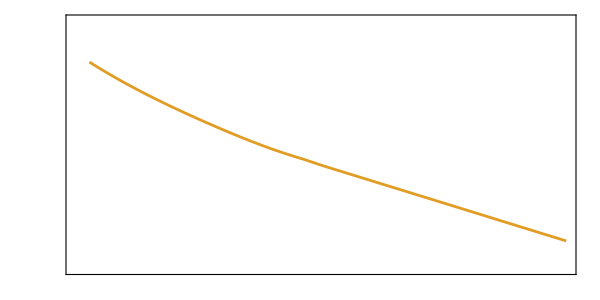

```mathematica
Plot[Log10[meanTypeIaCDLInterp[10^logmatchlight]],{logmatchlight,1.5,5},Frame->True,Axes->False,PlotRange->{{1.4,Log10[10^5]},{-3,Log10[2*10^-1]}},
PlotStyle->color[2],
FrameTicks->{{logTick[-3,3,1.5,1],logTickNone[-3,3,1.5,1]},{logTick[2,6,1.5,1],None(*dMaxTab*)}},FrameStyle->Directive[{Black,AbsoluteThickness[1.5]}],FrameTicksStyle->Directive[{Black,AbsoluteThickness[.75]}],FrameLabel->{{MaTeX["
\\text{Error Budget }H_0
",Magnification->1.5],None},
{MaTeX["\\text{Interferometer Matchlight}",Magnification->1.5]
(*MaTeX["\\text{Matchlight }\\equiv [1 \\, \\rm{meter^2/picosecond^{1/2}}]",Magnification->1.5]*),
None}},ImageSize->600,AspectRatio->1/2,
ImagePadding->{{80,20},{70,70}}]
```

```mathematica
n2Sigma=2;
n4Sigma=4;
```

```mathematica
√(σSH0ESCDL3^2+σSH0ESCDLSystematics^2)
```

0.005

```mathematica
matchlight2SigmaSolutionCDLRung2=First[findAllRoots[meanTypeIaCDLInterp[matchlight]^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2-σPlanckSH0ESDiscrepancy^2/n2Sigma^2,{matchlight,10^2,10^5}]]
```

109.511

```mathematica
meanCepheidCDLInterp[107]
```

0.11591

```mathematica
matchlight3SigmaSolutionCDLRung2=First[findAllRoots[meanTypeIaCDLInterp[matchlight]^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2-σPlanckSH0ESDiscrepancy^2/n4Sigma^2,{matchlight,10^2.4,10^5}]]
```

401.647

```mathematica
√(meanTypeIaCDLInterp[1250]^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2)
√(meanTypeIaCDLInterp[50000]^2+σSH0ESCDL3^2+σSH0ESCDLSystematics^2)
```

0.0113219

0.00554633

```mathematica
(*Export[NotebookDirectory[]<>"optimumCepheidSigmaMuPlot.pdf",optimumσΔμCepheidPlot]*)
```